The goal of this notebook is simply to collect and organize all of the work that Vijay has already done in the various other Mathematica notebooks. This will hopefully be useful as a check by a second pair of eyes, and as a confirmation that all of our numbers and plots are up-to-date and final with our current understanding of physics.

```mathematica
ConvertMeV2ToMeVPerTrigger=Quantity[1.,"Megaelectronvolts"]^2/Quantity[1/10^-5,("Megaelectronvolts")/("Centimeters")] Quantity[1.,"SpeedOfLight"*"ReducedPlanckConstant"]^-1//UnitConvert
```

506773.

```mathematica
ConvertBarnToMeV=Quantity[1.,"Barns"]/Quantity[1.,("Megaelectronvolts")^-2] Quantity[1.,"SpeedOfLight"*"ReducedPlanckConstant"]^-2//UnitConvert
```

0.00256819

# Scratch

```mathematica
(8 π^5)/(15(2π)^3)//N
```

0.657974

```mathematica
EFermiMeV[0.85]
```

0.973853

```mathematica
nIonMeV[0.85]
λThomasFermi[0.85]

nIonMeV[1.37]
λThomasFermi[1.37]
```

0.00519886

15.0635

1.15996

2.4836

```mathematica
ryanω=(2q(q-p Cos[θin])Sin[α/2]^2 ee+p(-2(p-q Cos[θin])Sin[α/2]^2 ei+q Sin[α]Sin[θin] √(-p^2-q^2+2p q Cos[θin]+(ee+ei)^2)))/(p^2+q^2-2 p q Cos[θin]-(ee+ei)^2);
```

```mathematica
myω=(-(-1+cosθ) (E2 p1^2-E1 p2^2)+(-1+cosθ) (E1-E2) p1 p2 Cos[ψ]-√(1-cosθ^2)  p1 p2 Cos[ϕ] √(E1^2+2 E1 E2+E2^2-p1^2-p2^2-2 p1 p2 Cos[ψ]) Sin[ψ])/(E1^2+2 E1 E2+E2^2-p1^2-p2^2-2 p1 p2 Cos[ψ]);
```

```mathematica
ryanω/.{q->p1,p->p2,ee->E2,ei->E1,θin->ψ,α->θ}//FullSimplify
myω/.cosθ->Cos[θ]//FullSimplify[#,θ>0]&
```

(2 (-E2 p1^2+E1 p2^2+(-E1+E2) p1 p2 Cos[ψ]) Sin[θ/2]^2-p1 p2 √((E1+E2)^2-p1^2-p2^2+2 p1 p2 Cos[ψ]) Sin[θ] Sin[ψ])/((E1+E2)^2-p1^2-p2^2+2 p1 p2 Cos[ψ])

```mathematica
-(E1 p2 2 Sin[θ/2]^2 (p2+p1 Cos[ψ])-E2 p1 2 Sin[θ/2]^2 (p1+p2 Cos[ψ])-p1 p2 Abs[Sin[θ]] Cos[ϕ] √((E1+E2)^2-p1^2-p2^2-2 p1 p2 Cos[ψ]) Sin[ψ])/(-(E1+E2)^2+p1^2+p2^2+2 p1 p2 Cos[ψ])//FullSimplify
```

-(2 (-E2 p1^2+E1 p2^2+(E1-E2) p1 p2 Cos[ψ]) Sin[θ/2]^2-p1 p2 Abs[Sin[θ]] Cos[ϕ] √((E1+E2)^2-p1^2-p2^2-2 p1 p2 Cos[ψ]) Sin[ψ])/(-(E1+E2)^2+p1^2+p2^2+2 p1 p2 Cos[ψ])

```mathematica
cosψ->-cosψ
```

```mathematica
(-1+Cos[θ])+2 Sin[θ/2]^2//FullSimplify
```

0

```mathematica
(-(-1+cosθ) (-E1 p2^2)+(-1+cosθ) (E1) p1 p2 Cos[ψ]-√(1-cosθ^2)  p1 p2 Cos[ϕ] E1 Sin[ψ])/(E1^2)
```

```mathematica
nElectronCGS[1.26]
nElectronMeV[1.26]
λThomasFermi[1.26]
```

9.75341×10^31

0.703145

5.33251

```mathematica
(Z^2 α)/n^(-1/3)/.{Z->ZCarbon,α->αval,n->nIonMeV[1.37]}
```

36/137 nIonMeV[1.37]^(1/3)

```mathematica
cs(6π n)^(1/3)/.{cs->0.01,n->nIonMeV[1.37]}
```

0.0266134 nIonMeV[1.37]^(1/3)

```mathematica
Quantity[10^7,"Kelvin"]Quantity[1,"BoltzmannConstant"]//UnitConvert[#,"Kiloelectronvolts"]&//N
```

0.861733 keV

```mathematica
{y->ϵ/ω0,κ->√((2m y)/ω0),Q21->1/A(√y-√(y-n))^2,Q22->1/A(√y+√(y-n))^2,A->M/m,M->10^4,m->10^3,ω0->10^-2.}
```

```mathematica
Integrate[Exp[-Q2]/(Q2+η2)^2 Q2^n/(n!),{Q2,0,∞},Assumptions->{η2>0,n>0}]
```

(-1+ⅇ^η2 (n+η2) ExpIntegralE[n,η2])/n

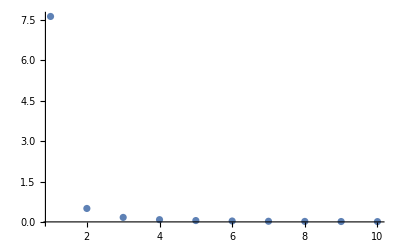

```mathematica
ListPlot[Table[{n,(-1+ⅇ^η2 (n+η2) ExpIntegralE[n,η2])/n/.η2->10^-4},{n,1,10}],PlotRange->All]
```

```mathematica
intvalueScreened[n_,κInMeV_]:=Module[{},
(* must have   k - ω > Ef   =>   u < κ - Ef/ω0 *)
Return[If[u>κ-Ef/ω0//.{Ef->(3 π^3 ne)^(1/3),ne->Z ni,Z->6,ni->1},
0,
If[(u^2 ω0)/(2 M)<η2&&((2 κ-u)^2 ω0)/(2 M)>η2,
(Gamma[1+n,Q21]-Gamma[1+n,Q22])/(η2^2 n!)+(Gamma[-1+n,Q22]-Gamma[-1+n,Q23])/(n!)//.{Q21->(u^2 ω0)/(2 M),Q22->η2,Q23->((u-2 κ)^2 ω0)/(2 M),u->n},
If[(u^2 ω0)/(2M)>η2,(Gamma[-1+n,Q21]-Gamma[-1+n,Q22])/(n!)//.{Q21->(u^2 ω0)/(2 M),Q22->((u-2 κ)^2 ω0)/(2 M)},
"Invalid"]
]]/.{u->n,ω0->10^-2,M->10^4,η2->10^-4,κ->κInMeV/10^-2}]
]
```

```mathematica
partialSumResults=Monitor[Table[{k,Sum[N[n*intvalueScreened[n,k]],{n,1,50k}]},{k,{10,20,30,40,50,60,70,80,90,100,150,200,250,300,350,400}}],{k}]
```

{{10,10.4005},{20,11.7853},{30,12.5944},{40,13.1679},{50,13.6122},{60,13.9749},{70,14.2813},{80,14.5464},{90,14.7801},{100,14.9888},{150,15.7902},{200,16.356},{250,16.793},{300,17.1484},{350,17.4476},{400,17.7056}}

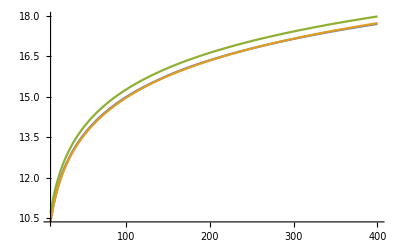

```mathematica
partialSumApprox=Interpolation[partialSumResults];
Plot[{partialSumApprox[k],5.75+Log[k^2/1],Log[(4.7337245221906464*^11 k^2)/(4.00000001*^8+80000. k)]-1},{k,10,400},PlotRange->All]
```

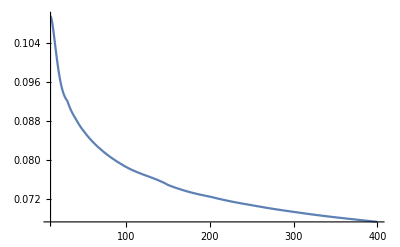

```mathematica
Plot[{Abs[partialSumApprox[k]-Log[(4.7337245221906464*^11 k^2)/(4.00000001*^8+80000. k)]]/Log[(4.7337245221906464*^11 k^2)/(4.00000001*^8+80000. k)]},{k,10,400},PlotRange->All]
```

```mathematica
λThomasFermi[1.37,6]
```

λThomasFermi[1.37,6]

```mathematica
Log[((2M k^2/m^2)/(1+2k M/m^2+(M/m)^2))/Max[(Z^2 α^2)/(b^2 M)/.b->((6π Z α ne)/Ef)^(-1/2)]]//.{M->10^4,m->.5,Z->6,α->1/137.,ne->Z ni,ni->1,Ef->(3 π^2 ne)^(1/3)}
```

Log[(4.73372×10^11 k^2)/(4.×10^8+80000. k)]

```mathematica
Max[(Z^2 α^2)/(b^2 M)/.b->((6π Z α ne)/Ef)^(-1/2)]//.{M->10^4,m->.5,Z->6,α->1/137.,ne->Z ni,ni->1,Ef->(3 π^2 ne)^(1/3)}
```

1.69×10^-7

Total cross section:

```mathematica
partialSumsForTotalCrossSection=Monitor[Table[{k,Sum[N[intvalueScreened[n,k]],{n,1,50k}]},{k,{10,20,30,40,50,60,70,80,90,100,150,200,250,300,350,400}}],{k}]
```

{{10,9.65091},{20,10.0077},{30,10.0773},{40,10.1016},{50,10.1129},{60,10.1191},{70,10.1228},{80,10.1252},{90,10.1269},{100,10.128},{150,10.1309},{200,10.1318},{250,10.1323},{300,10.1326},{350,10.1327},{400,10.1328}}

```mathematica
1/((2π Z^2 α^2)/(M β^2))Integrate[(2π Z^2 α^2)/(M β^2)1/ω^2(1-β^2 ω/ωKIN),{ω,ωMIN,ωKIN},Assumptions->{ωMIN>0,ωKIN>ωMIN}]//FullSimplify
```

(ωKIN-ωMIN-β^2 ωMIN Log[ωKIN/ωMIN])/(ωKIN ωMIN)

```mathematica
Evaluate[{(ωKIN-ωMIN-β^2 ωMIN Log[ωKIN/ωMIN])/(ωKIN ωMIN),10/ω0}//.{ω0->.01,ωKIN->(2M k^2/m^2)/(1+2k M/m^2+(M/m)^2),ωMIN->(Z^2 α^2)/(b^2 M),b->((6π Z α ne)/Ef)^(-1/2),M->10^4,m->.5,Z->6,α->1/137.,ne->Z ni,ni->1,Ef->(3 π^2 ne)^(1/3)}]
```

{1/k^2 73.9644 (4.×10^8+80000. k) (-1.69×10^-7+(80000. k^2)/(4.×10^8+80000. k)-1.69×10^-7 β^2 Log[(4.73372×10^11 k^2)/(4.×10^8+80000. k)]),1000.}

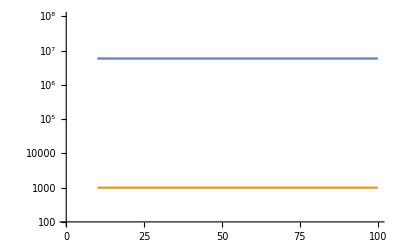

```mathematica
LogPlot[Evaluate[{(ωKIN-ωMIN-β^2 ωMIN Log[ωKIN/ωMIN])/(ωKIN ωMIN),10/ω0}//.{ω0->.01,ωKIN->(2M k^2/m^2)/(1+2k M/m^2+(M/m)^2),ωMIN->(Z^2 α^2)/(b^2 M),b->((6π Z α ne)/Ef)^(-1/2),M->10^4,m->.5,Z->6,α->1/137.,ne->Z ni,ni->1,Ef->(3 π^2 ne)^(1/3),β->1}],{k,10,100},PlotRange->{10^2,10^8}]
```

```mathematica
Integrate[ω(2π Z^2 α^2)/(M β^2)1/ω^2(β^2 ω/ωKIN),{ω,ωMIN,ωKIN},Assumptions->{ωMIN>0,ωKIN>ωMIN}]
```

(2 π Z^2 α^2 (ωKIN-ωMIN))/(M ωKIN)

```mathematica
Integrate[ω(2π Z^2 α^2)/(M β^2)1/ω^2(1),{ω,ωMIN,ωKIN},Assumptions->{ωMIN>0,ωKIN>ωMIN}]
```

(2 π Z^2 α^2 Log[ωKIN/ωMIN])/(M β^2)

# White dwarf parameters

Here we define various physical parameters of the white dwarf, which are used frequently in this notebook. They are defined as functions of white dwarf mass or density, where appropriate.

Let’s say that the following are the minimum and maximum white dwarf masses of interest, which are ultimately what we care about for plotting and discussion.

```mathematica
Mmin=0.85;
Mmax=1.37;
```

Some useful values:

```mathematica
mCarbon=12*10^3(* MeV *);
ZCarbon=6;
αval=1/137;
mNeutron=940;
mProton=938;
mPion=140;
mElectron=0.5;
```

## White dwarf mass and radius data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/priggins/Dropbox/Berkeley-current/Research/WhiteDwarfParticleDetector/Qballs

Density-mass relation and number densities

## Density-mass relation

Density-mass relation and its inverse, with density in g/cm^3 and mass in M_☉.

```mathematica
WDLogDensityMassData=Import["WD.csv"];
WDDensityMassData={10^(#[[1]]),#[[2]]}&/@WDLogDensityMassData;
WDDensityMassCGS=Interpolation[WDDensityMassData]
WDMassDensityCGS=Interpolation[Reverse/@WDDensityMassData]
```

10
InterpolatingFunction[{{11437.4, 5.43438 10  }}, <>]

InterpolatingFunction[{{0.0405266, 1.40072}}, <>]

Similarly, with densities in units of MeV^4,

```mathematica
Quantity[1.,"Grams"/("Centimeters")^3]/Quantity[1.,("Megaelectronvolts")^4/(("SpeedOfLight")^5("ReducedPlanckConstant")^3)]//UnitConvert
```

4.31013×10^-6

```mathematica
WDDensityMassDataInMeV={Quantity[#[[1]],"Grams"/("Centimeters")^3]/Quantity[1.,("Megaelectronvolts")^4/(("SpeedOfLight")^5("ReducedPlanckConstant")^3)],#[[2]]}&/@WDDensityMassData;
WDDensityMassMeV=Interpolation[WDDensityMassDataInMeV]
WDMassDensityMeV=Interpolation[Reverse/@WDDensityMassDataInMeV]
```

InterpolatingFunction[{{0.0492968, 234229.}}, <>]

InterpolatingFunction[{{0.0405266, 1.40072}}, <>]

Some example densities as functions of mass:

```mathematica
{WDMassDensityCGS[0.85],WDMassDensityCGS[1.25],WDMassDensityCGS[1.37]}
{WDMassDensityMeV[0.85],WDMassDensityMeV[1.25],WDMassDensityMeV[1.37]}
```

{1.44744×10^7,2.88397×10^8,3.22949×10^9}

{62.3864,1243.03,13919.5}

## Ion and electron number densities

We know compute the ion and electron number densities as a function of white dwarf mass. Note that our ions are carbon with mass = 12*m_p and charge Z=6.

### Ion number density

In units of cm^-3,

```mathematica
nIonCGS[M_]:=WDMassDensityCGS[M] Quantity[1.,"Grams"]/Quantity[12,"ProtonMass"];
Table[nIonCGS[M],{M,{0.85,1.25,1.37}}]
```

{7.21141×10^29,1.43685×10^31,1.609×10^32}

And in units of MeV^3,

```mathematica
nIonMeV[M_]:=WDMassDensityMeV[M] Quantity[1.,"Megaelectronvolts"]/Quantity[12,"Gigaelectronvolts"];
Table[nIonMeV[M],{M,{0.85,1.25,1.37}}]
```

{0.00519886,0.103586,1.15996}

```mathematica
nIonMeV[1.4]
```

13.7133

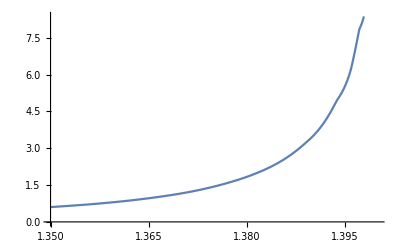

```mathematica
Plot[nIonMeV[Mwd],{Mwd,1.35,1.4}]
```

### Electron number density

In units of cm^-3,

```mathematica
nElectronCGS[M_]:=nIonCGS[M]*Z/.{Z->ZCarbon};
Table[nElectronCGS[M],{M,{0.85,1.25,1.37}}]
```

{4.32685×10^30,8.62111×10^31,9.65397×10^32}

And in units of MeV^3,

```mathematica
nElectronMeV[M_]:=nIonMeV[M]*Z/.{Z->ZCarbon};
Table[nElectronMeV[M],{M,{0.85,1.25,1.37}}]
```

{0.0311932,0.621515,6.95976}

In the Fermi sea, the electron number density is reduced. A particle transferring energy ω to an electron in the Fermi sea sees an effective electron density of

```mathematica
Integrate[ϵ^2/π^2,{ϵ,Ef-ω,Ef}]//FullSimplify
```

(ω (3 Ef^2-3 Ef ω+ω^2))/(3 π^2)

Note when ω=E_f, this is the full electron density:

```mathematica
Integrate[ϵ^2/π^2,{ϵ,0,Ef}]/.Ef->(3 π^2 ne)^(1/3)
```

ne

So we can define an effective density

```mathematica
nElectronEffective[ω_,Mwd_]:=Piecewise[{
{nElectronMeV[Mwd],ω≥EFermiMeV[Mwd]},
{(ω (3 Ef^2-3 Ef ω+ω^2))/(3 π^2)/.Ef->EFermiMeV[Mwd],ω<EFermiMeV[Mwd]}
}];
```

This is given approximately by a linear reduction below the Fermi energy:

```mathematica
nElectronEffectiveApprox[electronEnergy_,Mwd_]:=Piecewise[{
{nElectronMeV[Mwd],electronEnergy≥EFermiMeV[Mwd]},
{nElectronMeV[Mwd] electronEnergy/EFermiMeV[Mwd],electronEnergy<EFermiMeV[Mwd]}
}];
```

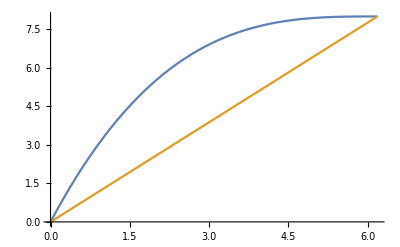

```mathematica
PlotTEMP[{(ω (3 Ef^2-3 Ef ω+ω^2))/(3 π^2),n ω/Ef},{ω,0,Ef}]//.{Ef->(3 π^2 n)^(1/3),n->8}/.PlotTEMP->Plot
```

Mass-radius relation and escape velocity

## Mass-radius relation

Mass-radius relation and its inverse, with mass in M_☉ and radius in km. (The radius is originally in R_☉ in the data file, which must be converted.).

```mathematica
WDMassRadiusData=Import["WDradius.csv"];
WDMassRadiusDataConvertedToKilometers={1,Quantity[1.,"SolarRadius"]/Quantity[1.,"Kilometers"]}*#&/@WDMassRadiusData;
WDMassRadius=Interpolation[WDMassRadiusDataConvertedToKilometers]
WDRadiusMass=Interpolation[Reverse/@WDMassRadiusDataConvertedToKilometers]
```

InterpolatingFunction[{{0.0407984, 1.42331}}, <>]

InterpolatingFunction[{{328.863, 19770.4}}, <>]

## Escape velocity

Here is the escape velocity as a fraction of c, again as a function of white dwarf mass.

```mathematica
vesc[M_]:=1/c √((2G Mwd)/R)/.
{G->Quantity[1.,"GravitationalConstant"],
R->Quantity[WDMassRadius[M],"Kilometers"],
Mwd->Quantity[M,"SolarMass"],
c->Quantity[1.,"SpeedOfLight"]}//UnitConvert;
Table[vesc[M],{M,{0.85,1.25,1.37}}]
```

{0.0198225,0.0333143,0.0463183}

## Plasma and Lattice parameters

Fermi energy:

```mathematica
EFermiMeV[Mwd_]:=(3 π^2 nElectronMeV[Mwd])^(1/3);
```

Thomas-Fermi length:

```mathematica
λThomasFermi[Mwd_]:=(Ef/(6π α ne))^(1/2)/.{Ef->EFermiMeV[Mwd],ne->nElectronMeV[Mwd],α->αval};
```

Plasma frequency ( = Debye temperature):

```mathematica
ΩPlasma[Mwd_]:=√((4 π n Z^2 α)/M)/.{n->nIonMeV[Mwd],α->αval,Z->ZCarbon,M->mCarbon}
```

```mathematica
ΩPlasma[1.37]
ΩPlasma[0.85]
```

0.017866

0.00119608

Plasma parameter:

```mathematica
ΓPlasma[Mwd_,TwdInKeV_]:=(Z^2 α)/(n^(-1/3)T)/.{n->nIonMeV[Mwd],α->αval,Z->ZCarbon,T->TwdInKeV/10^3.}
```

```mathematica
ΓPlasma[1.37,1]
ΓPlasma[0.85,1]
```

276.098

45.5217

```mathematica
ΓPlasma[1.37,10]
ΓPlasma[0.85,10]
```

27.6098

4.55217

# Trigger size and boom energies

Here we calculate the trigger size and minimum energy deposits necessary for explosion as functions of white dwarf density and mass.

## Trigger size

Here is the trigger size in cm^-3 as a function of white dwarf density and mass:

```mathematica
Clear@triggerMass
```

```mathematica
(*triggerSizeVersusDensityCGS[ρCGS_]:=
Return@If[ρCGS>10^8,10^-5*(ρCGS/(5*10^9))^(-1/2),1/(10000 √2)*(ρCGS/10^8)^-2];
triggerSizeVersusMass[M_]:=Module[{ρ},
ρ=WDMassDensityCGS[M];
Return@If[ρ>10^8,10^-5*(ρ/(5*10^9))^(-1/2),1/(10000 √2)*(ρ/10^8)^-2]
];*)
triggerSizeVersusDensityCGS[ρCGS_]:=
Piecewise[{{10^-5*(ρCGS/(5*10^9))^(-1/2),ρCGS>10^8},{1/(10000 √2)*(ρCGS/10^8)^-2,ρCGS<10^8}}];
triggerSizeVersusMass[M_]:=Module[{ρ},
ρ=WDMassDensityCGS[M];
Piecewise[{{10^-5*(ρ/(5*10^9))^(-1/2),ρ>10^8},{1/(10000 √2)*(ρ/10^8)^-2,ρ<10^8}}]
];
```

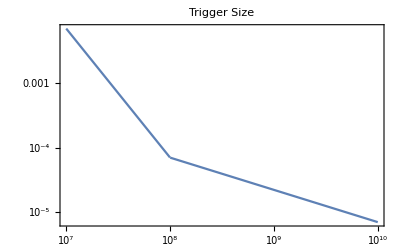

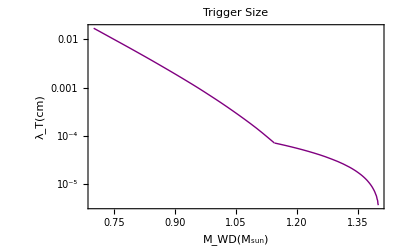

```mathematica
LogLogPlot[{triggerSizeVersusDensityCGS[ρ]},{ρ,10^10,10^7},PlotLabel->"Trigger Size",Frame->True]
LogPlot[triggerSizeVersusMass[M],{M,0.7,1.4},PlotLabel->"Trigger Size",Frame->True,PlotStyle->{Thick,Purple},FrameLabel->{"M_WD(M_sun)","λ_T(cm)"},FrameStyle->Black]
```

```mathematica
Table[Quantity[triggerMass[M],"Centimeters"],{M,{0.85,1.25,1.37}}]//ScientificForm
```

{3.3751×10^-3 cm,4.1638×10^-5 cm,1.24428×10^-5 cm}

## E_boom

The minimum energy deposit necessary to explode the white dwarf is given here in GeV as a function of white dwarf mass:

```mathematica
eboom[M_]:=Log10[(nIonCGS[M]*(4π)/3(λT)^3 Tmin)/Quantity[1.,"Gigaelectronvolts"]]/.{λT->triggerMass[M],Tmin->Quantity[1.,"Megaelectronvolts"]};
```

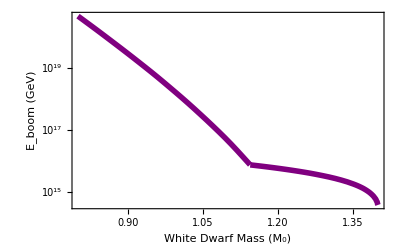

```mathematica
XLabelEboom = {{0.2, "0.2"},{0.3, "0.3"},{0.4, "0.4"},{0.5, "0.5"}, {0.6, "0.6"},{0.7, "0.7"},  {0.8, "0.8"},{0.9, "0.9"}, {1.0, "1.0"},{1.1, "1.1"}, {1.2, "1.2"},{1.3, "1.3"}, {1.4, "1.4"}}; 
YLabelEboom = {{15, "10^15"}, {16, "10^16"},{17, "10^17"}, {18, "10^18"}, {19, "10^19"},  {20, "10^20"},{21, "10^21"},{22, "10^22"},{23, "10^23"}}; 
YEboom = {{15, ""}, {16, ""},{17, ""}, {18, ""}, {19, ""},  {20,""},{21, ""},{22, ""},{23, ""}};
Eboom=Plot[eboom[M],{M,0.8,1.40},Frame->True,FrameTicks-> {{YLabelEboom,YEboom},{Automatic,None}},FrameLabel->{"White Dwarf Mass (M_0)","E_boom (GeV)"},FrameStyle->Black,PlotStyle-> {Purple,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```

```mathematica
Table[Quantity[10^eboom[M],"Gigaelectronvolts"],{M,{0.85,1.25,1.37}}]
```

{1.16136×10^20 GeV,4.34479×10^15 GeV,1.29837×10^15 GeV}

# Collision processes and stopping powers

Here we gather and compute the stopping powers for all the various collision processes (Coulomb, hadronic shower, etc.) that energetic particles in a white dwarf might undergo.

## Nuclear interactions

Low-energy elastic scatters

Once pions and nucleons have sufficiently low-energy (below 10 MeV), they can hadronically scatter of ions either elastically (transferring a fraction of their kinetic energy and then bouncing off).

## Bounce-counting method

At this point, the particles are non-relativistic. Conservation of momentum and energy demands

```mathematica
Solve[{1/2 m vi^2==1/2 m vf^2+1/2 M v^2,m vi==m vf Cos[θ]+M v Cos[ψ],0==m vf Sin[θ]-M v Sin[ψ]},vf,{ψ,v}]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{vf→(2 m vi Cos[θ]-√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))},{vf→(2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))}}

The second solution is the physical one, so the incident particle has final energy

```mathematica
Efin=1/2 m((2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M)))^2/.vi->Sqrt[2 ϵ/m];
```

assuming the incident particle had initial energy ϵ. The incident particle retains a fraction of its initial energy given by

```mathematica
Eretained=FullSimplify[Efin/ϵ,Assumptions->{ϵ>0,M>0,m>0}];
```

The average fraction ζ retained, considering all possible angles of scatter and assuming the particle scatters isotopically, is

```mathematica
ζel=1/(2Pi)Integrate[Eretained,{θ,0,2Pi},Assumptions->{ϵ>0,M>0,m>0}]//FullSimplify
```

M^2/(m+M)^2

A proper calculation (lab frame angle not exactly isotropic, unlike CM angle) yields ζ= (M^2+m^2)/(m+M)^2~M^2/(m+M)^2for heavy nuclei, so our estimate here is good.

Since a light incident particle retains most of its energy after collision with a heavy incident particle, it will perform a random walk with several collisions before it has transferred O(1) of its initial energy. The number of steps nn is

```mathematica
Solve[ζel^nn==0.1/.{M->mCarbon,m->mPion},nn]//Quiet(* pion *)
```

{{nn→99.2568}}

```mathematica
Solve[ζel^nn==0.1/.{M->mCarbon,m->mNeutron},nn]//Quiet(* neutron/proton, ignoring electromagnetic scatters *)
```

{{nn→15.2658}}

Since this is a random walk, the particle will travel a distance √nn λ, where λ=(n_ion σ)^-1 is the mean free path. The stopping powers are therefore

```mathematica
dEdxElasticMesonBounceCounting=Piecewise[{{ϵ/(nn(nion*σElasticMeson)^-1)/.nn->100,ϵ≤10},{0,ϵ>10}}];
dEdxElasticNucleonBounceCounting=Piecewise[{{ϵ/(nn(nion*σElasticNucleon)^-1)/.nn->10,ϵ≤10},{0,ϵ>10}}];
```

## Free particle structure factor method

At this point, the particles are non-relativistic. Conservation of momentum and energy demands

```mathematica
Solve[{1/2 m vi^2==1/2 m vf^2+1/2 M v^2,m vi==m vf Cos[θ]+M v Cos[ψ],0==m vf Sin[θ]-M v Sin[ψ]},vf,{ψ,v}]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{vf→(2 m vi Cos[θ]-√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))},{vf→(2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))}}

The second solution is the physical one, so the incident particle has final energy

```mathematica
Efin=1/2 m((2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M)))^2/.vi->Sqrt[2 ϵ/m];
Efin//FullSimplify
```

(m (√2 m √(ϵ/m) Cos[θ]+√(-m ϵ+(2 M^2 ϵ)/m+m ϵ Cos[2 θ]))^2)/(2 (m+M)^2)

The maximum energy transfer is

```mathematica
ϵ-Efin/.θ->π//FullSimplify[#,M>0]&
```

(4 m M ϵ)/(m+M)^2

The free particle dσ/dω for a non-relativistic neutron scattering on targets of mass M is given by

```mathematica
dσdωNeutronElastic=(2π M b^2)/k^2/.b->√(σ/(4π))
```

(M σ)/(2 k^2)

Note σ is approximately the total free particle scattering cross section:

```mathematica
σFreeNeutron=Integrate[dσdωNeutronElastic/.k->√(2m ϵ),{ω,0,(4 m M ϵ)/(m+M)^2}]
```

(M^2 σ)/(m+M)^2

The stopping power is then

```mathematica
Integrate[dσdωNeutronElastic n ω/.k->√(2m ϵ),{ω,0,(4 m M ϵ)/(m+M)^2}]
```

(2 m M^3 n ϵ σ)/(m+M)^4

Or in terms of the free cross section σ_f,

```mathematica
(2 m M^3 n ϵ σ)/(m+M)^4/.First@Solve[σFreeNeutron==σf,σ]
```

(2 m M n ϵ σf)/(m+M)^2

For a neutron or proton, the stopping power is

```mathematica
(2 m M n ϵ σf)/(m+M)^2/.{M->mCarbon,m->mNeutron}//N
```

0.134732 n ϵ σf

For a pion,

```mathematica
(2 m M n ϵ σf)/(m+M)^2/.{M->mCarbon,m->mPion}//N
```

0.0227983 n ϵ σf

These very similar to the bounce-counting results.

## Plots

Putting the stopping powers in a for amenable to plotting (using the structure factor results), we find for neutrons and protons

```mathematica
Clear@dEdxElasticPion
```

```mathematica
dEdxElasticNucleon[ϵ_,Mwd_]:=Piecewise[{{(2 m M n ϵ σf)/(m+M)^2,1<ϵ<10},{0,ϵ>10}}]/.{M->mCarbon,m->mNeutron,n->nIonMeV[Mwd],σf->1*ConvertBarnToMeV};
```

and for pions

```mathematica
dEdxElasticPion[ϵ_,Mwd_]:=Piecewise[{{(2 m M n ϵ σf)/(m+M)^2,1<ϵ<10},{0,ϵ>10}}]/.{M->mCarbon,m->mPion,n->nIonMeV[Mwd],σf->1*ConvertBarnToMeV};
```

Nucleon plot matches well ....

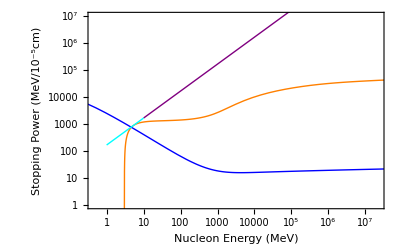
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxElasticNucleon[ϵ,1.37],{ϵ,1,10}],-Graphics-]
```

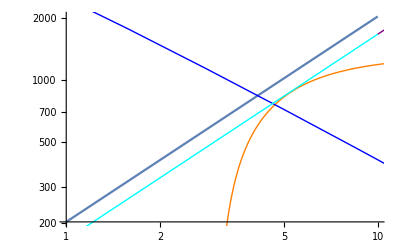

as does the pion plot ...

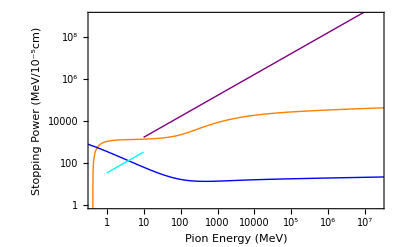
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxElasticPion[ϵ,1.37],{ϵ,1,10}],-Graphics-]
```

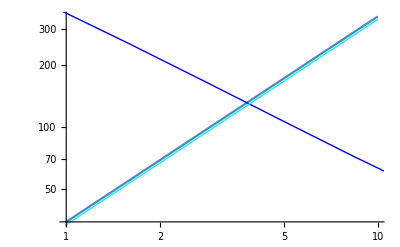

### Low densities

```mathematica
nElectronMeV[0.85]
```

0.0311932

Nucleon plot matches well ....

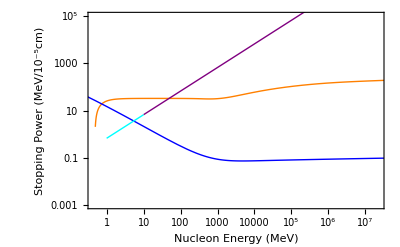
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxElasticNucleon[ϵ,0.85],{ϵ,1,10}],-Graphics-]
```

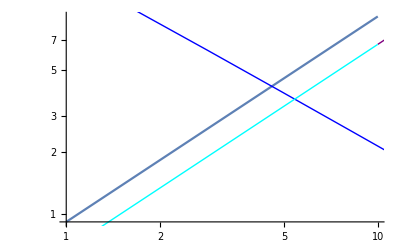

as does the pion plot ...

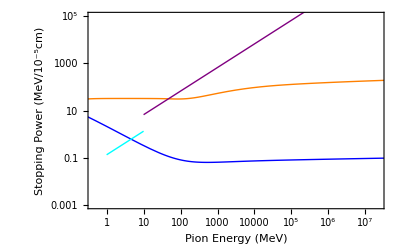
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxElasticPion[ϵ,0.85],{ϵ,1,10}],-Graphics-]
```

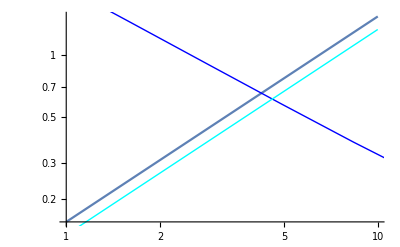

Low-energy inelastic scatters

In principle, a neutron or pion could also be inelastically absorbed by the ion. The neutron capture cross section for carbon is famously low, which is why it is useful as a moderator for nuclear reactors. There is a 3 order of magnitude difference between the scattering and capture cross-sections for neutrons in carbon.

As for pions ...... also probably insignificant compared to elastic scatters.

Phonon production

Not important.

Nonelastic scatters / Hadronic showers

When the energy is too high, the particles will non-elastically scatter instead, disintegrating the ions they hit:

```mathematica
dEdxNonelastic[ϵ_,Mwd_]:=Piecewise[{{ϵ/(n*σNonelastic)^-1,ϵ>10},{0,ϵ≤10}}]/.{n->nIonMeV[Mwd],σNonelastic->0.1*ConvertBarnToMeV};
```

Nucleons match well ...

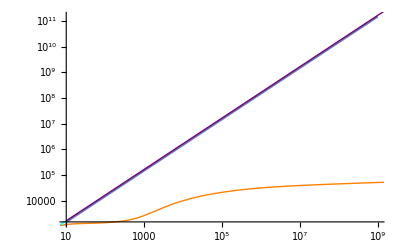

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxNonelastic[ϵ,1.37],{ϵ,10,10^9}],-Graphics-]
```

As do pions .... (good, because it’s the same curve ...)

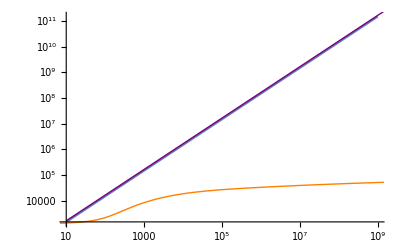

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxNonelastic[ϵ,1.37],{ϵ,10,10^9}],-Graphics-]
```

### low densities

Nucleons match well ...

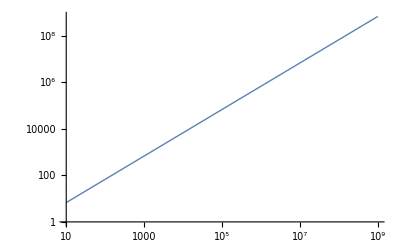

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxNonelastic[ϵ,0.85],{ϵ,10,10^9},PlotStyle->Thick]
```

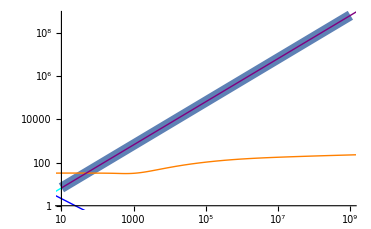

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxNonelastic[ϵ,0.85],{ϵ,10,10^9},PlotStyle->Thickness[.02]],-Graphics-]
```

As do pions .... (good, because it’s the same curve ...)

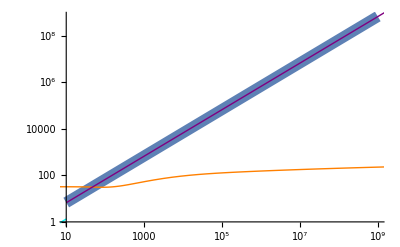

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxNonelastic[ϵ,0.85],{ϵ,10,10^9},PlotStyle->Thickness[.02]],-Graphics-]
```

Photonuclear and electronuclear interactions

## Photonuclear

At high enough energies, photons can produce quark-anti-quark pairs and disintegrate a nucleus. The corresponding stopping power is

```mathematica
dEdxPhotonuclear[ϵ_,Mwd_]:=Piecewise[{{ϵ/(n*σγA)^-1,ϵ>10},{0,ϵ≤10}}]/.{n->nIonMeV[Mwd],σγA->0.001*ConvertBarnToMeV};
```

This matches well.

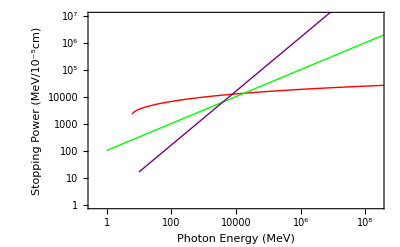
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxPhotonuclear[ϵ,1.37],{ϵ,10,10^9}],-Graphics-]
```

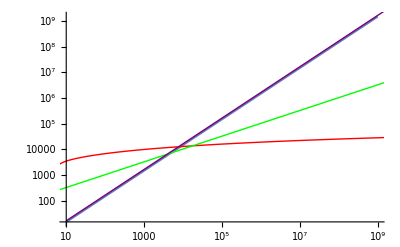

### low densities

This matches well.

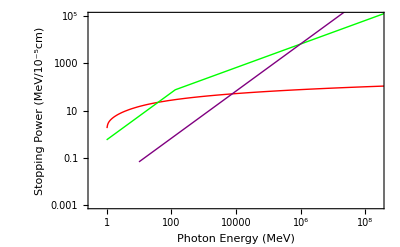
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxPhotonuclear[ϵ,0.85],{ϵ,10,10^9},PlotStyle->Thickness[0.02]],-Graphics-]
```

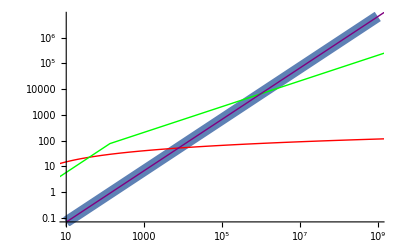

## Electronuclear

At high enough energies, electrons can produce virtual photons that can disintegrate a nucleus via photonuclear interaction. The corresponding stopping power is

```mathematica
dEdxElectronuclear[ϵ_,Mwd_]:=Piecewise[{{ϵ/(n*σeA)^-1,ϵ>10},{0,ϵ≤10}}]//.{n->nIonMeV[Mwd],σeA->10α σγA,α->αval,σγA->0.001*ConvertBarnToMeV};
```

This matches well.

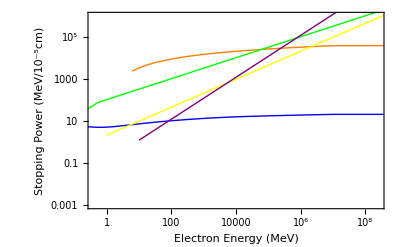
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxElectronuclear[ϵ,1.37],{ϵ,10,10^9}],-Graphics-]
```

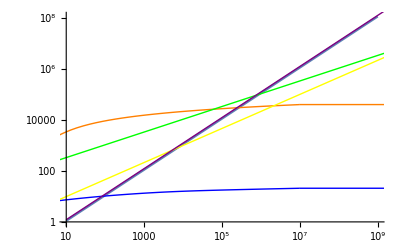

### low densities

This matches well.

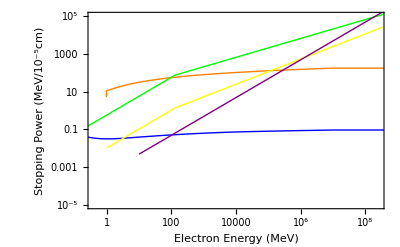
```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxElectronuclear[ϵ,0.85],{ϵ,10,10^9},PlotStyle->Thickness[0.02]],-Graphics-]
```

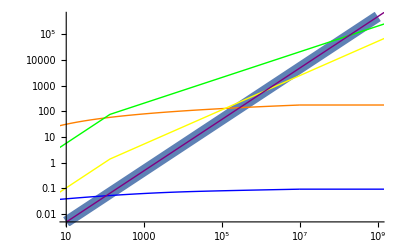

## EM Radiative processes

Bremsstrahlung (with LPM)

## Electrons

The cross-section for an election of energy ϵ to radiate a photon of energy k is given by the Bethe-Heitler formula

```mathematica
dσBHdkBremNoLPM=1/(3k n X0)(y^2+2(1+(1-y)^2))/.{y->k/ϵ};
```

where X_0=(4n Z^2 α^3/m_e^2 Log[Λ])^-1 is the radiation length and log Λ ∼ ∫1/b is a logarithmic form factor containing the maximum and minimum effective impact parameters allowed in the scatter. Integrating for the stopping power

```mathematica
dEdxBremElectronNoLPM[ϵ_]=Integrate[dσBHdkBremNoLPM*k*n,{k,Min[ϵ-Ef,ϵ^2/(ELPM+ϵ)],ϵ-Ef}]//FullSimplify
```

Piecewise[{{(-Ef^3 (ELPM+ϵ)^3+Ef^2 ϵ (ELPM+ϵ)^3-3 Ef ϵ^2 (ELPM+ϵ)^3+ELPM ϵ^3 (3 ELPM^2+5 ELPM ϵ+3 ϵ^2))/(3 X0 ϵ^2 (ELPM+ϵ)^3), Ef<(ELPM ϵ)/(ELPM+ϵ)}, {0, True}}]

For the log, the max impact parameter is set by the screening length, and the min by the Compton wavelength. Here we see the “brem shutoff” at all but very low densities .... but we’ll ignore this and assume logΛ ~ 1 like Vijay has in his calculations, assuming this isn’t something to worry about.

```mathematica
Log[bmax/bmin]//.{bmax->λThomasFermi[Mwd],bmin->(2π)/mElectron,Mwd->0.4586,Z->ZCarbon}
```

0.896003

```mathematica
X0BremElectron[Mwd_]:=(4n Z^2 α^3/me^2 logΛ)^-1/.{n->nIonMeV[Mwd],Z->ZCarbon,α->αval,me->mElectron,logΛ->1};
```

At high incident energies LPM suppression becomes relevant. This modifies the cross section at high energies (E>E_LPM) to be

```mathematica
dσBHdkBremWithLPM=√((ELPM k)/(ϵ(ϵ-k)))1/(3k n X0)(y^2+2(1+(1-y)^2))/.{y->k/ϵ};
```

for an LPM-suppressed stopping power

```mathematica
int=Integrate[dσBHdkBremWithLPM*k*n,{k,0,x},Assumptions->{x>0,ϵ>x}];
dEdxBremElectronLPMPart[ϵ_]=int/.x->Min[ϵ-Ef,ϵ^2/(ELPM+ϵ)];
```

No we have limited the upper bound to avoid dipping into the Fermi sea.

The LPM energy is

```mathematica
ELPMBremElectron[Mwd_]:=(me^2 X0 α)/(4π)/.{me->mElectron,α->αval,X0->X0BremElectron[Mwd]};
```

and we find the full stopping power to be

```mathematica
dEdxBremElectron[ϵ_,Mwd_]:=Piecewise[{{dEdxBremElectronNoLPM[ϵ],ϵ<ELPM},{dEdxBremElectronLPMPart[ϵ],ϵ>ELPM}}]/.{X0->X0BremElectron[Mwd],ELPM->ELPMBremElectron[Mwd],Ef->EFermiMeV[Mwd]};
dEdxBremElectronSimple[ϵ_,Mwd_]:=Piecewise[{{ϵ/X0BremElectron[Mwd] √(ELPMBremElectron[Mwd]/ϵ),ϵ>ELPMBremElectron[Mwd]&&ϵ>EFermiMeV[Mwd]},{ϵ/X0BremElectron[Mwd],EFermiMeV[Mwd]<ϵ<ELPMBremElectron[Mwd]},{0,ϵ<EFermiMeV[Mwd]}}];
```

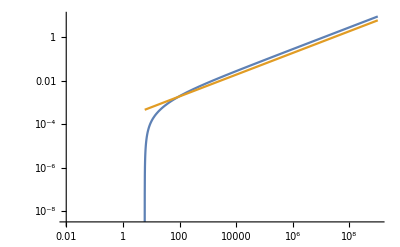

```mathematica
LogLogPlot[Evaluate[{dEdxBremElectron[ϵ,Mwd]/.Mwd->1.37,dEdxBremElectronSimple[ϵ,Mwd]/.Mwd->1.37}],{ϵ,.01,10^9}]
```

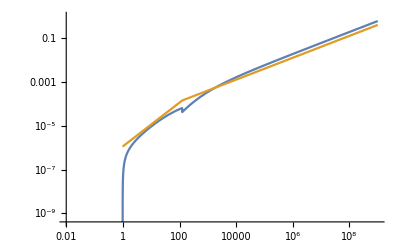

```mathematica
LogLogPlot[Evaluate[{dEdxBremElectron[ϵ,Mwd]/.Mwd->0.85,dEdxBremElectronSimple[ϵ,Mwd]/.Mwd->0.85}],{ϵ,.01,10^9}]
```

Comparing with Vijay’s result ... good match, mine is about a factor of 3 higher because I kept the prefactor in the LPM-suppressed stopping power

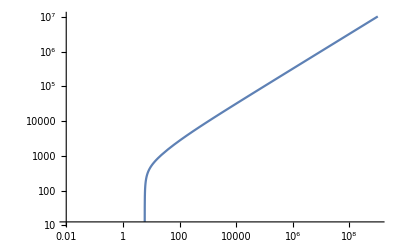
```mathematica
Show[-Graphics-,-Graphics-]
```

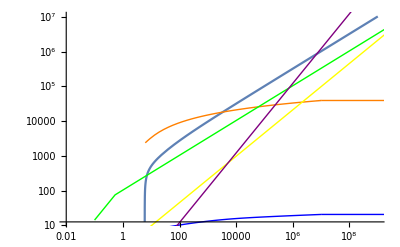

#### Low densities

This again matches well, again differing by a factor of 3-4.

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxBremElectron[ϵ,Mwd]/.Mwd->0.85,{ϵ,.01,10^9}],-Graphics-]
```

$Aborted

## Pions

The bremsstrahlung stopping power for pions is the same as that for electrons except for the rent mounts and the lack of any degeneracy concerns.

The cross-section is still

```mathematica
dσBHdkBremNoLPM=1/(3k n X0)(y^2+2(1+(1-y)^2))/.{y->k/ϵ};
```

where X_0=(4n Z^2 α^3/m_π^2 Log[Λ])^-1 is the radiation length and log Λ ∼ ∫1/b is a logarithmic form factor containing the maximum and minimum effective impact parameters allowed in the scatter. Integrating for the stopping power

```mathematica
dEdxBremPionNoLPM[ϵ_]=Integrate[dσBHdkBremNoLPM*k*n,{k,0,ϵ}]//FullSimplify
```

ϵ/X0

For the log, the max impact parameter is set by the screening length, and the min by the Compton wavelength. Here we see no shut off at any density, and in general logΛ~few.

```mathematica
Log[bmax/bmin]//.{bmax->λThomasFermi[Mwd],bmin->(2π)/mPion,Mwd->1.37}
```

4.01347

```mathematica
X0BremPion[Mwd_]:=(4n Z^2 α^3/mπ^2 logΛ)^-1//.{n->nIonMeV[Mwd],Z->ZCarbon,α->αval,mπ->mPion,
logΛ->Log[bmax/bmin],bmax->λThomasFermi[Mwd],bmin->(2π)/mPion};
```

At high incident energies LPM suppression becomes relevant. This modifies the cross section at high energies (E>E_LPM) to be again

```mathematica
dσBHdkBremWithLPM=√((ELPM k)/(ϵ(ϵ-k)))1/(3k n X0)(y^2+2(1+(1-y)^2))/.{y->k/ϵ};
```

for an LPM-suppressed stopping power

```mathematica
dEdxBremPionLPMPart[ϵ_]=Integrate[dσBHdkBremWithLPM*k*n,{k,0,ϵ},Assumptions->{ϵ>Ef,Ef>0}]//FullSimplify
```

(23 π √(ELPM ϵ))/(48 X0)

The LPM energy is

```mathematica
ELPMBremPion[Mwd_]:=(mπ^2 X0 α)/(4π)/.{mπ->mPion,α->αval,X0->X0BremPion[Mwd]};
ELPMBremPion[1.37]
ELPMBremPion[0.85]
```

8.55889×10^8

1.31779×10^11

and we find the full stopping power to be

```mathematica
dEdxBremPion[ϵ_,Mwd_]:=Piecewise[{{dEdxBremPionNoLPM[ϵ],ϵ<ELPM},{dEdxBremPionLPMPart[ϵ],ϵ>ELPM}}]/.{X0->X0BremPion[Mwd],ELPM->ELPMBremPion[Mwd]};
```

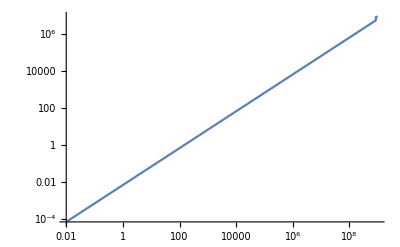

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxBremPion[ϵ,Mwd]/.Mwd->1.37,{ϵ,.01,10^9}]
```

Vijay has no results to compare this to

#### Low densities

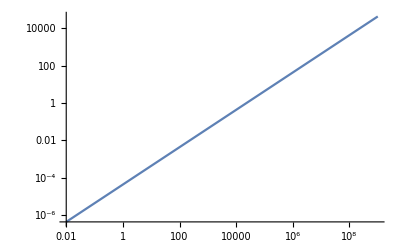

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxBremPion[ϵ,Mwd]/.Mwd->0.85,{ϵ,.01,10^9}]
```

Pair production (with LPM)

The cross-section for a photon of energy ϵ to radiate an electron-positron pair with energies e and ϵ-e is given by a similar Bethe-Heitler formula

```mathematica
dσBHdkPP=1/(3ϵ n X0)(1+2(x^2+(1-x)^2))/.{x->e/ϵ};
```

where X_0=(4n Z^2 α^3/me^2 Log[Λ_pp])^-1 is a similar radiation length, only the log being different. (What is it??) Integrating for the stopping power

```mathematica
dEdxPPNoLPM=Integrate[dσBHdkPP ϵ n,{e,0,ϵ}]//FullSimplify
```

(7 ϵ)/(9 X0)

For the log ........

```mathematica
Log[bmax/bmin]
```

Log[bmax/bmin]

```mathematica
X0PP[Mwd_]:=(4n Z^2 α^3/me^2 logΛpp)^-1/.{n->nIonMeV[Mwd],Z->ZCarbon,α->αval,me->mElectron,logΛpp->1};
```

At high incident energies LPM suppression becomes relevant. This modifies the cross section at high energies (E>E_LPM) to be

```mathematica
dσBHdkPPwithLPM=√((ELPM ϵ)/(e(ϵ-e)))1/(3ϵ n X0)(1+2(x^2+(1-x)^2))/.{x->e/ϵ};
```

for a new stopping power

```mathematica
dEdxPPLPMPart=Integrate[dσBHdkPPwithLPM ϵ n,{e,0,ϵ}]//FullSimplify
```

(5 π √(ELPM/ϵ) ϵ)/(6 X0)

The LPM energy is the same, except with the new radiation length (Is this true???),

```mathematica
ELPMPP[Mwd_]:=(me^2 X0 α)/(4π)/.{me->mElectron,α->αval,X0->X0PP[Mwd]};
```

and we find the full stopping power to be

```mathematica
dEdxPP[ϵ_,Mwd_]:=Piecewise[{{(7 ϵ)/(9 X0),2m≤ϵ<ELPM},{(5π)/6(ELPM/ϵ)^(1/2)ϵ/X0,ϵ>ELPM},{0,ϵ<2m}}]/.{X0->X0PP[Mwd],ELPM->ELPMPP[Mwd],m->mElectron};
```

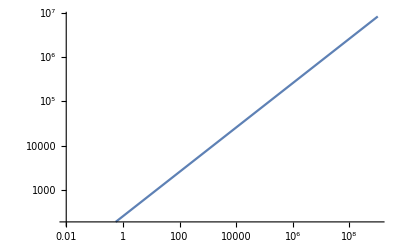

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxPP[ϵ,Mwd]/.Mwd->1.37,{ϵ,.01,10^9}]
```

Comparing with Vijay’s result ... good match, mine is about a factor of 3 higher because I kept the prefactor in the LPM-suppressed stopping power

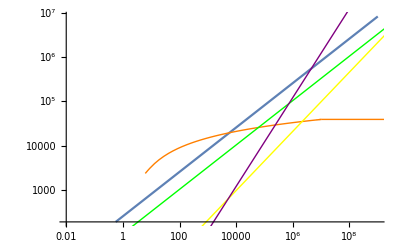

```mathematica
Show[-Graphics-,-Graphics-]
```

#### Low densities

Comparing with Vijay’s result ... good match, mine is about a factor of 3 higher because I kept the prefactor in the LPM-suppressed stopping power

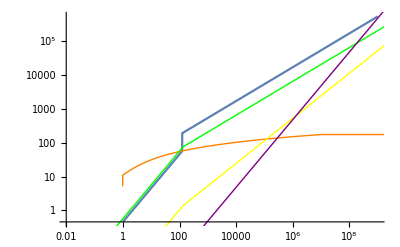

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxPP[ϵ,Mwd]/.Mwd->0.85,{ϵ,.01,10^9}],-Graphics-]
```

Direct pair production from electron scattering (with LPM)

Here we adapt directly the stopping power formula in Vijay’s notebook (no formulas are given explicitly in the paper) in a way to make it look similar to the previous radiative processes in this notebook. We find

```mathematica
dEdxDirectPP[ϵ_,Mwd_]:=Piecewise[{{(ELPM/ϵ)^(1/3)α ϵ/X0*3,ϵ≥ELPM},{α ϵ/X0*3,2m≤ϵ≤ELPM},{0,ϵ<2m}}]//.{X0->((4n Z^2 α^3)/m^2)^-1,ELPM->(m^2 X0 α)/(4π),α->αval,m->mElectron,Z->ZCarbon,n->nIonMeV[Mwd]}
```

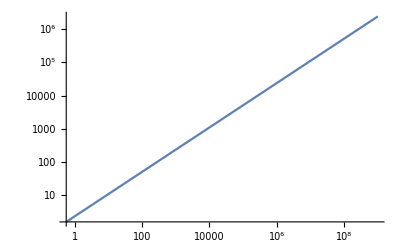

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxDirectPP[ϵ,Mwd]/.Mwd->1.37,{ϵ,.01,10^9},PlotRange->All]
```

This matches Vijay’s results well, as we should hope

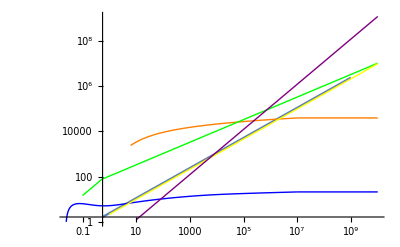

```mathematica
Show[-Graphics-,-Graphics-]
```

#### Low densities

This matches Vijay’s results well, as we should hope

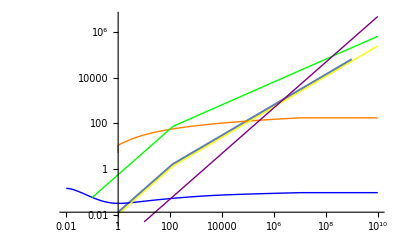

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxDirectPP[ϵ,Mwd]/.Mwd->0.85,{ϵ,.01,10^9},PlotRange->All],-Graphics-]
```

## Coulomb off ions

Coulomb collisions of hadrons off ions

The Coulomb energy transfer cross section for a target with charge ±1 scattering off an ion with charge Z is

```mathematica
dσdωCoulomb[ω_]:=(2π Z^2 α^2)/(M β^2)1/ω^2(1-β^2 ω/ωKIN);
```

Picking the max energy transfer as the kinematically allowed maximum, and the minimum as set by the screening length, we find

```mathematica
Integrate[(2π Z^2 α^2)/(M β^2)1/ω^2 n ω,{ω,ωSCR,ωKIN},Assumptions->{ωSCR>0,ωKIN>ωSCR}]//FullSimplify
```

(2 n π Z^2 α^2 Log[ωKIN/ωSCR])/(M β^2)

```mathematica
Integrate[dσdωCoulomb[ω]n ω,{ω,ωSCR,ωKIN},Assumptions->{ωSCR>0,ωKIN>ωSCR}]//FullSimplify
```

(2 n π Z^2 α^2 (β^2 (-ωKIN+ωSCR)+ωKIN Log[ωKIN/ωSCR]))/(M β^2 ωKIN)

So the stopping power is approximately

```mathematica
(2 n π Z^2 α^2)/(M β^2)(Log[ωKIN/ωSCR]-1)
```

(2 n π Z^2 α^2 (-1+Log[ωKIN/ωSCR]))/(M β^2)

but we will use the more exact form here:

```mathematica
dEdxCoulombHadronsOffIonsSymbolic=(2 n π Z^2 α^2 (β^2 (-ωKIN+ωSCR)+ωKIN Log[ωKIN/ωSCR]))/(M β^2 ωKIN);
```

The maximum kinematically allowed energy transfer (corresponding to a backwards scatter) is

```mathematica
ωkin[ϵ_,m_,M_]:=(2M β^2 γ^2)/(1+2γ M/m+(M/m)^2)//.{β->√(1-γ^-2),γ->ϵ/m+1};
```

#### [Derivation]

```mathematica
Solve[{√(ki^2+m^2)==√(kf^2+m^2)+√(p^2+M^2),ki==kf Cos[θ]+p Cos[ψ],0==kf Sin[θ]-p Sin[ψ]}/.θ->π,kf,{ψ,p}]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{kf→-(2 ki m^2-ki M^2+√(-(ki^2+m^2) M^2 (4 m^2-M^2)))/(2 m^2)},{kf→(√(-(ki^2+m^2) M^2 (4 m^2-M^2))+ki (-2 m^2+M^2))/(2 m^2)}}

```mathematica
√(ki^2+m^2)-√(kf^2+m^2)/.{kf->(√(-(ki^2+m^2) M^2 (4 m^2-M^2))+ki (-2 m^2+M^2))/(2 m^2)}//FullSimplify
```

√(ki^2+m^2)-√(m^2+((√(-(ki^2+m^2) M^2 (4 m^2-M^2))+ki (-2 m^2+M^2))^2)/(4 m^4))

```mathematica
Solve[{γi m+M==γf m+γM M,γi βi m==-γf βf m+γM βM M,γM==(1-βM^2)^(-1/2),γf==(1-βf^2)^(-1/2)},γf,{γM,βM,βf}]//FullSimplify
```

{{γf→((M+m γi) (m+2 M γi-m (-1+βi^2) γi^2)+√(m^2 βi^2 γi^2 (m-2 M (-1+γi)+m (-1+βi^2) γi^2) (m+m (-1+βi^2) γi^2-2 M (1+γi))))/(2 (M-m (-1+βi) γi) (M+m (1+βi) γi))},{γf→((M+m γi) (m+2 M γi-m (-1+βi^2) γi^2)-√(m^2 βi^2 γi^2 (m-2 M (-1+γi)+m (-1+βi^2) γi^2) (m+m (-1+βi^2) γi^2-2 M (1+γi))))/(2 (M-m (-1+βi) γi) (M+m (1+βi) γi))}}

```mathematica
m(γi-γf)/.{γf->((M+m γi) (m+2 M γi-m (-1+βi^2) γi^2)-√(m^2 βi^2 γi^2 (m-2 M (-1+γi)+m (-1+βi^2) γi^2) (m+m (-1+βi^2) γi^2-2 M (1+γi))))/(2 (M-m (-1+βi) γi) (M+m (1+βi) γi))}/.γi->(1-βi^2)^(-1/2)//FullSimplify[#,{γi>0,βi>0,m>0,M>0,βi<1}]&
```

-(2 m^2 M βi^2)/(-2 m M √(1-βi^2)+m^2 (-1+βi^2)+M^2 (-1+βi^2))

```mathematica
-(2 m^2 M β^2)/(-2 m M √(1-βi^2)+m^2 (-1+βi^2)+M^2 (-1+βi^2))/.βi->√(1-1/γ^2)//FullSimplify[#,γ>0]&
```

(2 m^2 M β^2 γ^2)/(m^2+M^2+2 m M γ)

#### [Continuing ...]

The minimum energy transfer (ignoring lattice effects) corresponds to a soft scatter at the screening length. Estimating the energy transfer between a particle of charge 1 scattering off a particle of charge Z as (Δp)^2/(2M)∼(F Δt)^2/(2M)∼(((Z α)/b^2(2b)/β)^2)/(2M), we find

```mathematica
ωscr[ϵ_,m_,M_,Mwd_]:=(2 Z^2 α^2)/(b^2 β^2 M)//.{b->λThomasFermi[Mwd],α->αval,Ef->EFermiMeV[Mwd],ne->nElectronMeV[Mwd],β->√(1-γ^-2),γ->ϵ/m+1}
```

So the stopping power is

```mathematica
dEdxCoulombHadronsOffIons[ϵ_,m_,Mwd_]:=dEdxCoulombHadronsOffIonsSymbolic//.
{ωSCR->ωscr[ϵ,m,M,Mwd],ωKIN->ωkin[ϵ,m,M],
M->mCarbon,Z->ZCarbon,n->nIonMeV[Mwd],
α->αval,Ef->EFermiMeV[Mwd],β->√(1-γ^-2),γ->ϵ/m+1};
```

### Pions off ions

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffIons[ϵ,mPion,1.37],{ϵ,.001,10^10},PlotRange->All]
```

$Aborted

Comparing to Vijay’s results, these match well

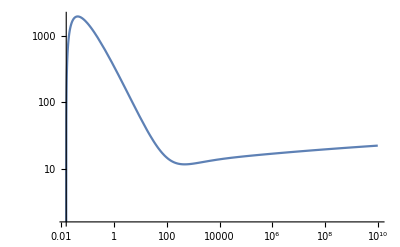
```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

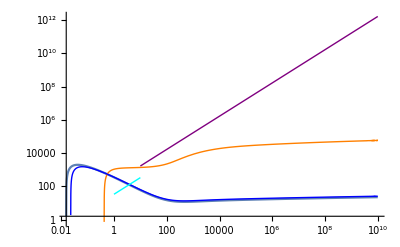

#### Low densities

Comparing to Vijay’s results, these match well

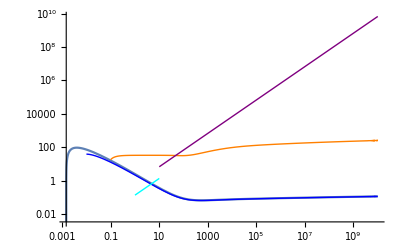

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffIons[ϵ,mPion,0.85],{ϵ,.0001,10^10},PlotRange->All],-Graphics-,PlotRange->All]
```

### Protons off ions

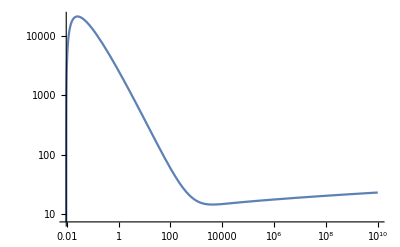

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffIons[ϵ,mProton,1.37],{ϵ,.001,10^10},PlotRange->All]
```

Comparing to Vijay’s results, these match well

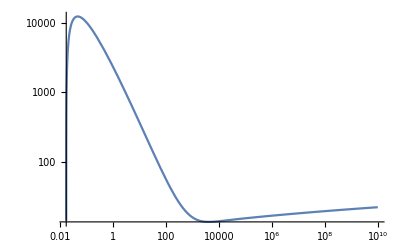
```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

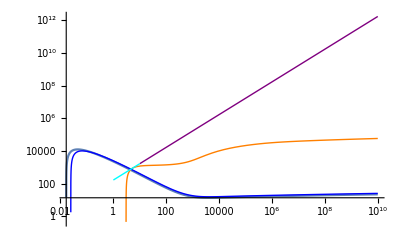

#### Low densities

Comparing to Vijay' s results, these match well

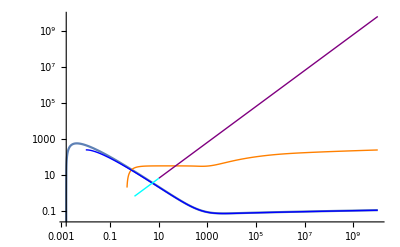

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffIons[ϵ,mProton,0.85],{ϵ,.001,10^10},PlotRange->All],-Graphics-,PlotRange->All]
```

Coulomb collisions of electrons off ions

The derivation here is similar to the one for hadrons off ions, except we need to account for the possible degeneracy of the electrons after scattering

The Coulomb energy transfer cross section for a target with charge ±1 scattering off an ion with charge Z is

```mathematica
dσdωCoulomb[ω_]:=(2π Z^2 α^2)/(M β^2)1/ω^2(1-β^2 ω/ωKIN);
```

Picking the max energy transfer as the kinematically allowed maximum OR the maximum before the target particle would fall below the Fermi sea (whichever is smaller), and the minimum as set by the screening length, we find

```mathematica
Integrate[dσdωCoulomb[ω]n ω,{ω,ωSCR,Min[ϵ-Ef,ωKIN]},Assumptions->{ωSCR>0,ωKIN>ωSCR,ϵ-Ef>ωSCR}]//FullSimplify
```

(2 n π Z^2 α^2 (β^2 ωSCR+ωKIN Log[Min[-Ef+ϵ,ωKIN]/ωSCR]-β^2 Min[-Ef+ϵ,ωKIN]))/(M β^2 ωKIN)

```mathematica
Integrate[dσdωCoulomb[ω]n ω,{ω,ωSCR,Min[Ωp,ωKIN]},Assumptions->{ωSCR>0,Ωp>ωSCR,ωKIN>ωSCR}]//FullSimplify
```

(2 n π Z^2 α^2 (β^2 ωSCR+ωKIN Log[Min[ωKIN,Ωp]/ωSCR]-β^2 Min[ωKIN,Ωp]))/(M β^2 ωKIN)

```mathematica
Integrate[dσdωCoulomb[ω]n ω,{ω,Min[Ωp,ωKIN],ωKIN},Assumptions->{ωSCR>0,Ωp>ωSCR,ωKIN>ωSCR}]//FullSimplify
```

(2 n π Z^2 α^2 (ωKIN (-β^2+Log[ωKIN/Min[ωKIN,Ωp]])+β^2 Min[ωKIN,Ωp]))/(M β^2 ωKIN)

So the stopping power is

```mathematica
dEdxCoulombElectronsOffIonsSymbolic[ϵ_]:=(2 n π Z^2 α^2 (β^2 ωSCR+ωKIN Log[Min[-Ef+ϵ,ωKIN]/ωSCR]-β^2 Min[-Ef+ϵ,ωKIN]))/(M β^2 ωKIN);
```

The kinematic maximum and screening energies are the same as before.

So the stopping power is

```mathematica
dEdxCoulombElectronsOffIons[ϵ_,Mwd_]:=dEdxCoulombElectronsOffIonsSymbolic[ϵ]//.
{ωSCR->ωscr[ϵ,m,M,Mwd],ωKIN->ωkin[ϵ,m,M],
m->mElectron,M->mCarbon,Z->ZCarbon,n->nIonMeV[Mwd],
α->αval,Ef->EFermiMeV[Mwd],β->√(1-γ^-2),γ->ϵ/m+1};
```

### Electrons off ions

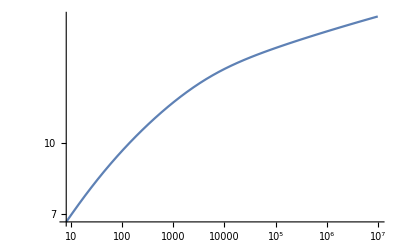

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombElectronsOffIons[ϵ,1.37],{ϵ,8,10^7}]
```

Comparing to Vijay’s results, we see they match pretty well. The difference seems to be entirely from me preserving the -1 with the log, though there are also slight differences in the densities we’re computing things at.

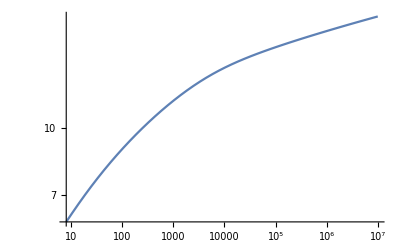
```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

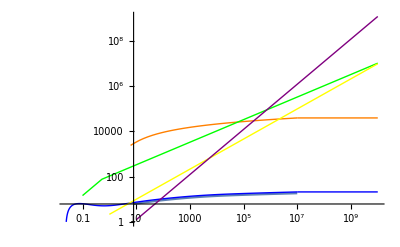

This is the same as if we had just used the hadron result, since the process is dominated by soft scatters:

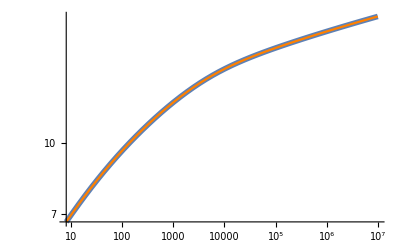

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombElectronsOffIons[ϵ,1.37],{ϵ,8,10^7},PlotStyle->Thickness[0.01]],
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffIons[ϵ,mElectron,1.37],{ϵ,8,10^7},PlotStyle->Orange]]
```

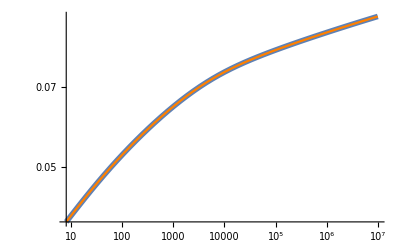

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombElectronsOffIons[ϵ,0.85],{ϵ,8,10^7},PlotStyle->Thickness[0.01]],
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffIons[ϵ,mElectron,0.85],{ϵ,8,10^7},PlotStyle->Orange]]
```

#### Low densities

Again these match well

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombElectronsOffIons[ϵ,0.85],{ϵ,8,10^7},PlotStyle->Thickness[0.02]],-Graphics-,PlotRange->All]
```

$Aborted

## Phonon production

Coulomb collisions of electrons off ions, with recoil

The derivation here is similar to the one for hadrons off ions, except we need to account for the possible degeneracy of the electrons after scattering

The Coulomb energy transfer cross section for a target with charge ±1 scattering off an ion with charge Z is

```mathematica
dσdcosθCoulombRecoil[θ_]:=(2π Z^2 α^2)/(4 ϵ^2 Sin[θ/2]^4)ϵprime/ϵ(Cos[θ/2]^2+(ϵ-ϵprime)/M Sin[θ/2]^2)/.ϵprime->ϵ/(1+ϵ/M(1-Cos[θ]));
```

```mathematica
ϵ-ϵprime/.ϵprime->ϵ/(1+ϵ/M(1-Cos[θ]))//FullSimplify
```

ϵ-(M ϵ)/(M+ϵ-ϵ Cos[θ])

```mathematica
intresult=Integrate[dσdcosθCoulombRecoil[θ]n(ϵ-ϵprime)Sin[θ]/.ϵprime->ϵ/(1+ϵ/M(1-Cos[θ])),{θ,θmin,π},Assumptions->{0<θmin<π,ϵ>0,M>0}];
```

```mathematica
result=intresult/.θmin->ArcCos[1+(ωSCR M)/((ωSCR-ϵ) ϵ)]//FullSimplify
```

1/(2 M ϵ^2 (M+2 ϵ)^2)n π Z^2 α^2 ((2 M^2+8 M ϵ+6 ϵ^2-M ωSCR-2 ϵ ωSCR) (M ωSCR+2 ϵ (-ϵ+ωSCR))-4 ϵ^2 (M+2 ϵ)^2 (Log[M+2 ϵ]-Log[(M ϵ)/(ϵ-ωSCR)]+Log[(M ωSCR)/(2 ϵ^2-2 ϵ ωSCR)]))

```mathematica
result
```

```mathematica
1/(2 M ϵ^2 (M+2 ϵ)^2)n π Z^2 α^2 ((2 M^2+8 M ϵ+6 ϵ^2) (2 ϵ (-ϵ))-4 ϵ^2 (M+2 ϵ)^2 (Log[(M+2 ϵ)/((M ϵ)/ϵ)(M ωSCR)/(2 ϵ^2)]))//FullSimplify
```

-(2 n π Z^2 α^2 ((M+ϵ) (M+3 ϵ)+(M+2 ϵ)^2 Log[((M+2 ϵ) ωSCR)/(2 ϵ^2)]))/(M (M+2 ϵ)^2)

```mathematica
-(2 n π Z^2 α^2 ((M+2 ϵ)^2+(M+2 ϵ)^2 Log[((M+2 ϵ) ωSCR)/(2 ϵ^2)]))/(M (M+2 ϵ)^2)//FullSimplify
```

-(2 n π Z^2 α^2 (1+Log[((M+2 ϵ) ωSCR)/(2 ϵ^2)]))/M

```mathematica
(2 n π Z^2 α^2 (Log[((2 M ϵ^2)/(M(M+2 ϵ)))/ωSCR]))/M
```

```mathematica
Log[M+2 ϵ]+Log[(me ωSCR)/(2 ϵ^2-2 ϵ ωSCR)]-Log[M+(me ωSCR)/(ϵ-ωSCR)]//FullSimplify
```

```mathematica
Log[((M+2 ϵ)(me ωSCR)/(2 ϵ^2-2 ϵ ωSCR))/(M+(me ωSCR)/(ϵ-ωSCR))]//FullSimplify
```

```mathematica
Log[(me (M+2 ϵ) ωSCR)/(2 ϵ (M ϵ))]
```

Log[(me (M+2 ϵ) ωSCR)/(2 M ϵ^2)]

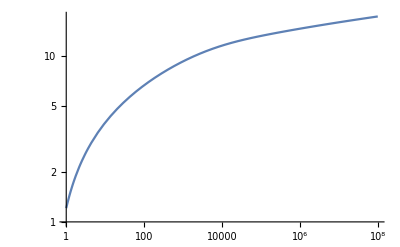

```mathematica
LogLogPlot[Evaluate[5*10^5*result//.{Z->ZCarbon,α->αval,n->nIonMeV[1.37], M->mCarbon,me->mElectron,ωSCR->μ^2/(2me),μ->1/λTF,λTF->λThomasFermi[1.37]}],{ϵ,1,10^8}]
```

So the stopping power is

```mathematica
dEdxCoulombElectronsOffIonsSymbolic[ϵ_]:=(2 n π Z^2 α^2 (β^2 ωSCR+ωKIN Log[Min[-Ef+ϵ,ωKIN]/ωSCR]-β^2 Min[-Ef+ϵ,ωKIN]))/(M β^2 ωKIN);
```

The kinematic maximum and screening energies are the same as before.

So the stopping power is

```mathematica
dEdxCoulombElectronsOffIons[ϵ_,Mwd_]:=dEdxCoulombElectronsOffIonsSymbolic[ϵ]//.
{ωSCR->ωscr[ϵ,m,M,Mwd],ωKIN->ωkin[ϵ,m,M],
m->mElectron,M->mCarbon,Z->ZCarbon,n->nIonMeV[Mwd],
α->αval,Ef->EFermiMeV[Mwd],β->√(1-γ^-2),γ->ϵ/m+1};
```

### Electrons off ions

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombElectronsOffIons[ϵ,1.37],{ϵ,8,10^7}]
```

-Graphics-

Comparing to Vijay’s results, we see they match pretty well. The difference seems to be entirely from me preserving the -1 with the log, though there are also slight differences in the densities we’re computing things at.

```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

-Graphics-

This is the same as if we had just used the hadron result, since the process is dominated by soft scatters:

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombElectronsOffIons[ϵ,1.37],{ϵ,8,10^7},PlotStyle->Thickness[0.01]],
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffIons[ϵ,mElectron,1.37],{ϵ,8,10^7},PlotStyle->Orange]]
```

-Graphics-

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombElectronsOffIons[ϵ,0.85],{ϵ,8,10^7},PlotStyle->Thickness[0.01]],
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffIons[ϵ,mElectron,0.85],{ϵ,8,10^7},PlotStyle->Orange]]
```

-Graphics-

#### Low densities

Again these match well

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombElectronsOffIons[ϵ,0.85],{ϵ,8,10^7},PlotStyle->Thickness[0.02]],-Graphics-,PlotRange->All]
```

$Aborted

## Phonon production

## Coulomb (off electrons) and Compton

Lab frame kinematics and energy transfer

```mathematica
ArbitraryBoost4Vec[AfourVec_,βvec_]:=Module[{A0,Avec,βsymbolSquared,γsymbol,newA0,newA3vec,newAfourVec},
A0=AfourVec[[1]];
Avec=Drop[AfourVec,1];
βsymbolSquared=βvec.βvec;
γsymbol=(1-βsymbolSquared)^(-1/2);
newA0=γsymbol(A0-βvec.Avec);
newA3vec=Avec+(γsymbol-1)/βsymbolSquared(βvec.Avec)βvec-γsymbol βvec A0;
newAfourVec=Prepend[newA3vec,newA0];
Return[newAfourVec];
]
```

```mathematica
YAxisRotation[AfourVec_,angle_]:=Module[{A0,Avec,newA3vec,newAfourVec},
A0=AfourVec[[1]];
Avec=Drop[AfourVec,1];
newA3vec=({{Cos[angle], 0, -Sin[angle]}, {0, 1, 0}, {Sin[angle], 0, Cos[angle]}}).Avec;
newAfourVec=Prepend[newA3vec,A0];
Return[newAfourVec];
];
```

```mathematica
AzimuthalRotation[AfourVec_,axisVec_,angle_]:=Module[{A0,Avec,axisUnitVec,newA3vec,newAfourVec},
A0=AfourVec[[1]];
Avec=Drop[AfourVec,1];
axisUnitVec=axisVec/(√(axisVec.axisVec));
newA3vec=(1-Cos[angle])(Avec.axisUnitVec)axisUnitVec+Cos[angle]Avec+Sin[angle](Cross[axisUnitVec,Avec]);
newAfourVec=Prepend[newA3vec,A0];
Return[newAfourVec];
];(*http://ksuweb.kennesaw.edu/~plaval//math4490/rotgen.pdf*)
```

```mathematica
kinsubs={E1->ϵ+M,E2->ϵe+m,p1->√(E1^2-M^2),p2->√(E2^2-m^2)};
trigsubs={Cos[θ]->cosθ,Sin[θ]->√(1-cosθ^2)};

p1FourVec={E1,p1 Sin[ψ/2],0,p1 Cos[ψ/2]};
p2FourVec={E2,-p2 Sin[ψ/2],0,p2 Cos[ψ/2]};
boostVec=(Drop[p1FourVec,1]+Drop[p2FourVec,1])/(p1FourVec[[1]]+p2FourVec[[1]]);
p1FourVecCOM=ArbitraryBoost4Vec[p1FourVec,boostVec];
p2FourVecCOM=ArbitraryBoost4Vec[p2FourVec,boostVec];
p3FourVec=ArbitraryBoost4Vec[AzimuthalRotation[YAxisRotation[p1FourVecCOM,θ],Drop[p1FourVecCOM,1],ϕ],-boostVec]//.trigsubs;
p4FourVec=ArbitraryBoost4Vec[AzimuthalRotation[YAxisRotation[p2FourVecCOM,θ],Drop[p1FourVecCOM,1],ϕ],-boostVec]//.trigsubs;
```

Energy transfer

```mathematica
ωtrans=p4FourVec[[1]]-p2FourVec[[1]];
(*ωtrans=-((-(-1+cosθ) (E2 p1^2-E1 p2^2)+(-1+cosθ) (E1-E2) p1 p2 Cos[ψ]-√(1-cosθ^2) p1 p2 √((E1+E2)^2-p1^2-p2^2-2 p1 p2 Cos[ψ]) Sin[ψ])/(-(E1+E2)^2+p1^2+p2^2+2 p1 p2 Cos[ψ]))//.kinsubs;*)
ωtrans=(-(-1+cosθ) (E2 p1^2-E1 p2^2)+(-1+cosθ) (E1-E2) p1 p2 Cos[ψ]-√(1-cosθ^2)  p1 p2 Cos[ϕ] √(E1^2+2 E1 E2+E2^2-p1^2-p2^2-2 p1 p2 Cos[ψ]) Sin[ψ])/(E1^2+2 E1 E2+E2^2-p1^2-p2^2-2 p1 p2 Cos[ψ])//.kinsubs;
```

CoM momentum

```mathematica
pCOMSquared=Module[{COMFourVec,COMvec},
COMFourVec=ArbitraryBoost4Vec[p1FourVec,boostVec];
COMvec=Drop[COMFourVec,1];
COMvec.COMvec
];
pCOMSquared=(2 E2^2 p1^2+(2 E1^2-p1^2) p2^2+p1 p2 (-4 E1 E2 Cos[ψ]+p1 p2 Cos[2 ψ]))/(2 ((E1+E2)^2-p1^2-p2^2-2 p1 p2 Cos[ψ]));
E1COM=Module[{COMFourVec,COMvec},
COMFourVec=ArbitraryBoost4Vec[p1FourVec,boostVec];
COMFourVec[[1]]
];
E1COM=(M^2+E1 E2-p1 p2 Cos[ψ])/(√((E1+E2)^2-p1^2-p2^2-2 p1 p2 Cos[ψ]));
E2COM=Module[{COMFourVec,COMvec},
COMFourVec=ArbitraryBoost4Vec[p2FourVec,boostVec];
COMFourVec[[1]]
];
E2COM=(m^2+E1 E2-p1 p2 Cos[ψ])/(√((E1+E2)^2-p1^2-p2^2-2 p1 p2 Cos[ψ]));
```

Incident and relative velocity

```mathematica
v=p1/E1//.kinsubs;
Clear[vrelCOM]
vrelCOM=(√pCOMSquared)/E1COM+(√pCOMSquared)/E2COM//.kinsubs;
```

Cross section

```mathematica
MMminimalMassivePhoton=Evaluate[(2 Z^2 e^4)/((t-μ^2)^2)(u^2+s^2+4 t(m^2+M^2)-2(m^2+M^2)^2)/.{s->(E1com+E2com)^2, t->-2 pcomSq(1-cosθ),u->(E1com-E2com)^2-2pcomSq(1+cosθ),e->√(4 π α),μ->1/λTF}];
MMmassivephoton=MMminimalMassivePhoton/.{E1com->E1COM,E2com->E2COM,pcomSq->pCOMSquared};
σCOMdcosθdϕmassivephoton=MMmassivephoton/(64 π^2(E1COM+E2COM)^2)//.kinsubs;

σCOMdcosθdϕElectron=α^2/(2s)(s^2/(t)^2+t^2/(s)^2+u^2(1/t+1/s)^2)/.{s->(E1com+E2com)^2, t->-2 pcomSq(1-cosθ),u->(E1com-E2com)^2-2pcomSq(1+cosθ),e->√(4 π α),μ->1/λTF}/.{E1com->E1COM,E2com->E2COM,pcomSq->pCOMSquared}//.kinsubs;
σCOMdcosθdϕmassivephotonElectron=α^2/(2s)(s^2/((t-μ^2)^2)+t^2/((s-μ^2)^2)+u^2(1/(t-μ^2)+1/(s-μ^2))^2)/.{s->(E1com+E2com)^2, t->-2 pcomSq(1-cosθ),u->(E1com-E2com)^2-2pcomSq(1+cosθ),e->√(4 π α),μ->1/λTF}/.{E1com->E1COM,E2com->E2COM,pcomSq->pCOMSquared}//.kinsubs;

MMminimalCompton=2 e^4(pkp/pk+pk/pkp+2 m^2(1/pk-1/pkp)+m^4(1/pk-1/pkp)^2)/.{pk->(s-m^2)/2,pkp->(u-m^2)/-2}/.{s->(E1com+E2com)^2, t->-2 pcomSq(1-cosθ),u->(E1com-E2com)^2-2pcomSq(1+cosθ),e->√(4 π α),μ->1/λTF};
MMCompton=MMminimalCompton/.{E1com->E1COM,E2com->E2COM,pcomSq->pCOMSquared};
σCOMdcosθdϕCompton=MMCompton/(64 π^2(E1COM+E2COM)^2)//.kinsubs;

σKNdcosθdϕCompton=α^2/(2 m^2)(kp/k)^2(kp/k+k/kp-Sin[θ]^2)/.trigsubs//.{kp->k/(1+k/m(1-cosθ)),k->E1COM}//.kinsubs;
σKNdcosθdϕComptonSymb=α^2/(2 m^2)(kp/k)^2(kp/k+k/kp-Sin[θ]^2)/.trigsubs//.{kp->k/(1+k/m(1-cosθ))};
```

Lab frame scattering rate

```mathematica
γiLab=(1-(p1/E1)^2)^(-1/2)//.kinsubs;
γeLab=(1-(p2/E2)^2)^(-1/2)//.kinsubs;
γiCOM=(1-pCOMSquared/E1COM^2)^(-1/2)//.kinsubs;
γeCOM=(1-pCOMSquared/E2COM^2)^(-1/2)//.kinsubs;
gammacombo=1/E1 1/E2((M^2+E1 E2-p1 p2 Cos[ψ])(m^2+E1 E2-p1 p2 Cos[ψ]))/((E1+E2)^2-p1^2-p2^2-2 p1 p2 Cos[ψ])//.kinsubs;
dNdtLab=gammacombo neEff σCOMdcosθdϕ vrelCOM;
dNdtLabMassivePhoton=gammacombo neEff σCOMdcosθdϕmassivephoton vrelCOM;

dNdtLabElectron=gammacombo neEff σCOMdcosθdϕElectron vrelCOM;
dNdtLabMassivePhotonElectron=gammacombo neEff σCOMdcosθdϕmassivephotonElectron vrelCOM;

dNdtLabCompton=gammacombo neEff σCOMdcosθdϕCompton vrelCOM;
```

Fermi Sea

Electron effective number density and Fermi energy

```mathematica
neEff=(8 π)/(2 π)^3 pf(ϵe+m)/.{pf->√((ϵe+m)^2-m^2)};
ϵf=√((3 π^2 ne)^(2/3)+m^2)-m;
pf=(3 π^2 ne)^(1/3);
```

Stopping Power Results, high density

## pion

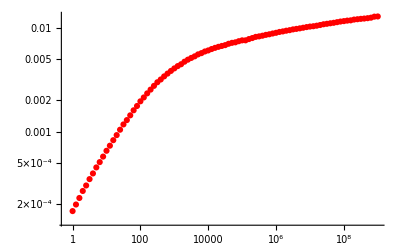

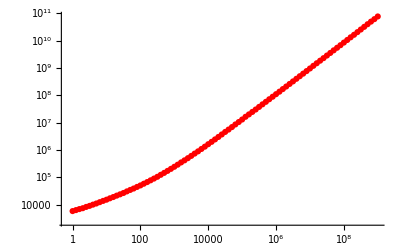

```mathematica
MwdVal=1.37;
numsubs={α->αval,Z->1,ne->nElectronMeV[MwdVal],M->mPion,m->mElectron,λTF->λThomasFermi[MwdVal]};
ϵvals=Table[10^(.1x),{x,0,90}];
expr=1/v 1/2 HoldIntegrate[Sin[ψ]dNdtLabMassivePhoton ωtrans HeavisideTheta[ωtrans-(ϵf-ϵe)],{ϕ,0,2π},{ψ,0,π},{ϵe,0,ϵf},{cosθ,-1,1},MaxPoints->100000,MinRecursion->5]//.numsubs;
pionHighDensityResults=Quiet@Monitor[Table[{ϵ,expr}/.HoldIntegrate->NIntegrate,{ϵ,ϵvals}],ϵ];
ListLogLogPlot[pionHighDensityResults,PlotRange->All,PlotStyle->Red]
ListLogLogPlot[{#[[1]],(#[[1]])/(#[[2]])}&/@pionHighDensityResults,PlotRange->All,PlotStyle->Red]
```

```mathematica
ryan=(2π Z^2 α^2 ne)/(m+Ef)(Integrate[1/ω(1-(1+(ω(ω-2Ef))/Pf^2)),{ω,0,Min[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}]+Integrate[1/ω,{ω,Min[ωkin,Ef],Max[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}])//FullSimplify
```

(ne π Z^2 α^2 (2 Pf^2 Log[Max[Ef,ωkin]/Min[Ef,ωkin]]+4 Ef Min[Ef,ωkin]-Min[Ef,ωkin]^2))/((Ef+m) Pf^2)

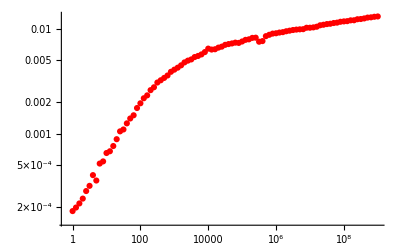
```mathematica
Show[-Graphics-,LogLogPlot[Evaluate[{
(2π Z^2 α^2 ne)/ϵf/.numsubs,
3/2 ryan//.{Ef->ϵf,Pf->pf,ωkin->(2m vel^2 γ^2)/(1+2γ m/M+(m/M)^2),γ->(1-vel^2)^(-1/2),vel->(√(EE^2-M^2))/EE,EE->ϵ+M}/.numsubs,
1/4*3/2 ne (Z^2 α^2)/pf √((2ϵ)/M)*Ia/.{Ia->75}/.numsubs}],{ϵ,1,10^9}], PlotRange->All]
```

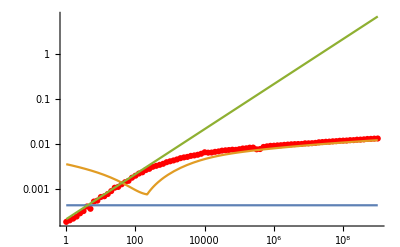

## proton

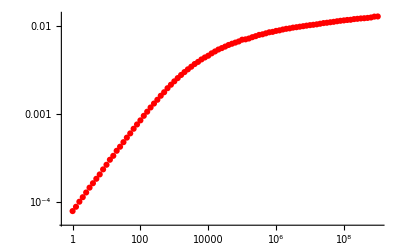

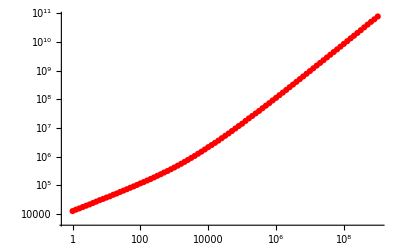

```mathematica
MwdVal=1.37;
numsubs={α->αval,Z->1,ne->nElectronMeV[MwdVal],M->mProton,m->mElectron,λTF->λThomasFermi[MwdVal]};
ϵvals=Table[10^(.1x),{x,0,90}];
expr=1/v 1/2 HoldIntegrate[Sin[ψ]dNdtLabMassivePhoton ωtrans HeavisideTheta[ωtrans-(ϵf-ϵe)],{ϕ,0,2π},{ψ,0,π},{ϵe,0,ϵf},{cosθ,-1,1},MaxPoints->100000,MinRecursion->5]//.numsubs;
protonHighDensityResults=Quiet@Monitor[Table[{ϵ,expr}/.HoldIntegrate->NIntegrate,{ϵ,ϵvals}],ϵ];
ListLogLogPlot[protonHighDensityResults,PlotRange->All,PlotStyle->Red]
ListLogLogPlot[{#[[1]],(#[[1]])/(#[[2]])}&/@protonHighDensityResults,PlotRange->All,PlotStyle->Red]
```

```mathematica
ryan=(2π Z^2 α^2 ne)/(m+Ef)(Integrate[1/ω(1-(1+(ω(ω-2Ef))/Pf^2)),{ω,0,Min[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}]+Integrate[1/ω,{ω,Min[ωkin,Ef],Max[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}])//FullSimplify
```

(ne π Z^2 α^2 (2 Pf^2 Log[Max[Ef,ωkin]/Min[Ef,ωkin]]+4 Ef Min[Ef,ωkin]-Min[Ef,ωkin]^2))/((Ef+m) Pf^2)

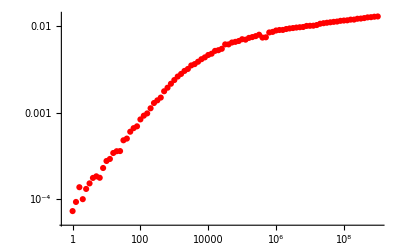
```mathematica
Show[-Graphics-,LogLogPlot[Evaluate[{
(2π Z^2 α^2 ne)/ϵf/.numsubs,
3/2 ryan//.{Ef->ϵf,Pf->pf,ωkin->(2m vel^2 γ^2)/(1+2γ m/M+(m/M)^2),γ->(1-vel^2)^(-1/2),vel->(√(EE^2-M^2))/EE,EE->ϵ+M}/.numsubs,
1/4*3/2 ne (Z^2 α^2)/pf √((2ϵ)/M)*Ia/.{Ia->75}/.numsubs}],{ϵ,1,10^9}], PlotRange->All]
```

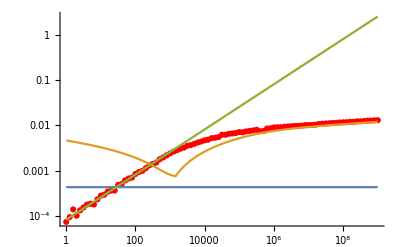

## ion

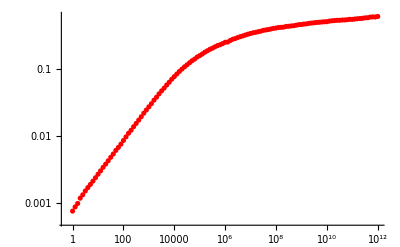

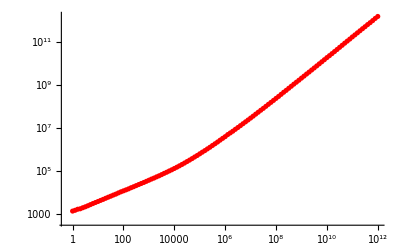

```mathematica
MwdVal=1.37;
numsubs={α->αval,Z->ZCarbon,ne->nElectronMeV[MwdVal],M->mCarbon,m->mElectron,λTF->λThomasFermi[MwdVal]};
ϵvalsLowϵ=Table[10^(.1x),{x,0,30}];
ϵvals=Table[10^(.1x),{x,31,120}];
expr1=1/v 1/2 HoldIntegrate[Sin[ψ]dNdtLabMassivePhoton ωtrans HeavisideTheta[ωtrans-(ϵf-ϵe)],{ϕ,0,2π},{ψ,0,π},{ϵe,0,ϵf},{cosθ,-1,1},MaxPoints->100000,MinRecursion->5]//.numsubs;
expr2=1/v 1/2 HoldIntegrate[Sin[ψ]dNdtLabMassivePhoton ωtrans HeavisideTheta[ωtrans-(ϵf-ϵe)],{ϕ,0,2π},{ψ,0,π},{ϵe,0,ϵf},{cosθ,-1,1},MaxPoints->100000,MinRecursion->5]//.numsubs;
ionHighDensityResultsLowϵ=Quiet@Monitor[Table[{ϵ,expr1}/.HoldIntegrate->NIntegrate,{ϵ,ϵvalsLowϵ}],ϵ];
ionHighDensityResults=ionHighDensityResultsLowϵ∪Quiet@Monitor[Table[{ϵ,expr2}/.HoldIntegrate->NIntegrate,{ϵ,ϵvals}],ϵ];
ListLogLogPlot[ionHighDensityResults,PlotRange->All,PlotStyle->Red]
ListLogLogPlot[{#[[1]],(#[[1]])/(#[[2]])}&/@ionHighDensityResults,PlotRange->All,PlotStyle->Red]
```

```mathematica
ryan=(2π Z^2 α^2 ne)/(m+Ef)(Integrate[1/ω(1-(1+(ω(ω-2Ef))/Pf^2)),{ω,0,Min[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}]+Integrate[1/ω,{ω,Min[ωkin,Ef],Max[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}])//FullSimplify
```

(ne π Z^2 α^2 (2 Pf^2 Log[Max[Ef,ωkin]/Min[Ef,ωkin]]+4 Ef Min[Ef,ωkin]-Min[Ef,ωkin]^2))/((Ef+m) Pf^2)

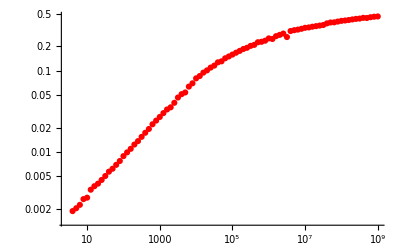
```mathematica
MwdVal=1.37;
numsubs={α->αval,Z->ZCarbon,ne->nElectronMeV[MwdVal],M->mCarbon,m->mElectron,λTF->λThomasFermi[MwdVal]};
Show[-Graphics-,LogLogPlot[Evaluate[{
(2π Z^2 α^2 ne)/ϵf/.numsubs,
3/2 ryan//.{Ef->ϵf,Pf->pf,ωkin->(2m vel^2 γ^2)/(1+2γ m/M+(m/M)^2),γ->(1-vel^2)^(-1/2),vel->(√(EE^2-M^2))/EE,EE->ϵ+M}/.numsubs,
1/4*3/2 ne (Z^2 α^2)/pf √((2ϵ)/M)*Ia/.{Ia->75}/.numsubs}],{ϵ,1,10^9}], PlotRange->All]
```

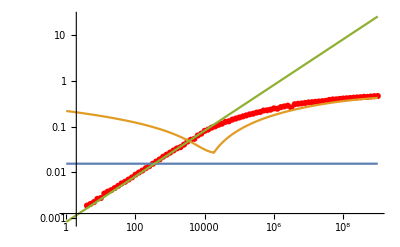

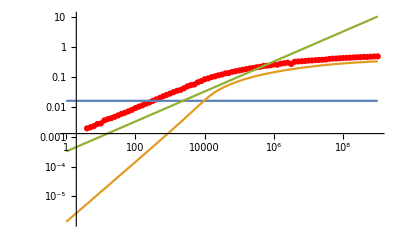

```mathematica
MwdVal=1.37;
numsubs={α->αval,Z->ZCarbon,ne->nElectronMeV[MwdVal],M->mCarbon,m->mElectron,λTF->λThomasFermi[MwdVal]};
Show[-Graphics-,LogLogPlot[Evaluate[{
(2π Z^2 α^2 ne)/ϵf/.numsubs,
ne (2π α^2 Z^2)/Ef G[ωKIN/Ef]//.{Ef->ϵf,Pf->pf,ωKIN->(2m vel^2 γ^2)/(1+2γ m/M+(m/M)^2),γ->(1-vel^2)^(-1/2),vel->(√(EE^2-M^2))/EE,EE->ϵ+M,G->Function[x,Piecewise[{{x^3/3-3/2 x^2+3x,x<1},{11/6+Log[x],x>1}}]]}/.numsubs,
ne (Z^2 α^2)/ϵf(√(2M ϵ))/M*Ia/.{Ia->10}/.numsubs}],{ϵ,1,10^9}], PlotRange->All]
```

## electron

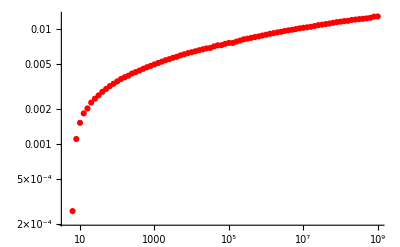

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

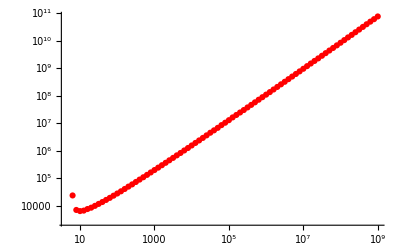

```mathematica
MwdVal=1.37;
numsubs={α->αval,Z->1,ne->nElectronMeV[MwdVal],M->mElectron,m->mElectron,λTF->λThomasFermi[MwdVal]};
ϵvals=Table[10^(.1x),{x,0,90}];
expr=1/v 1/2 HoldIntegrate[Sin[ψ]dNdtLabMassivePhotonElectron ωtrans HeavisideTheta[ωtrans-(ϵf-ϵe)]HeavisideTheta[(ϵ-ωtrans)-ϵf],{ϕ,0,2π},{ψ,0,π},{ϵe,0,ϵf},{cosθ,-1,1},MaxPoints->100000,MinRecursion->5]//.numsubs;
electronHighDensityResults=Quiet@Monitor[Table[{ϵ,expr}/.HoldIntegrate->NIntegrate,{ϵ,ϵvals}],ϵ];
ListLogLogPlot[electronHighDensityResults,PlotRange->All,PlotStyle->Red]
ListLogLogPlot[{#[[1]],(#[[1]])/(#[[2]])}&/@electronHighDensityResults,PlotRange->All,PlotStyle->Red]
```

```mathematica
ryan=(2π Z^2 α^2 ne)/(m+Ef)(Integrate[1/ω(1-(1+(ω(ω-2Ef))/Pf^2)),{ω,0,Min[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}]+Integrate[1/ω,{ω,Min[ωkin,Ef],Max[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}])//FullSimplify
```

(ne π Z^2 α^2 (2 Pf^2 Log[Max[Ef,ωkin]/Min[Ef,ωkin]]+4 Ef Min[Ef,ωkin]-Min[Ef,ωkin]^2))/((Ef+m) Pf^2)

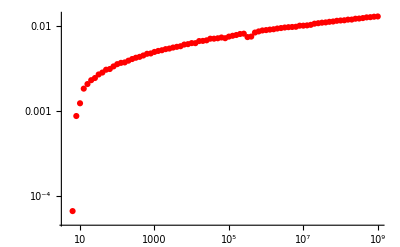
```mathematica
Show[-Graphics-,LogLogPlot[Evaluate[{
(2π Z^2 α^2 ne)/ϵf/.numsubs,
3/2 ryan//.{Ef->ϵf,Pf->pf,ωkin->(2m vel^2 γ^2)/(1+2γ m/M+(m/M)^2),γ->(1-vel^2)^(-1/2),vel->(√(EE^2-M^2))/EE,EE->ϵ+M}/.numsubs,
1/4*3/2 ne (Z^2 α^2)/pf √((2ϵ)/M)*Ia/.{Ia->75}/.numsubs}],{ϵ,1,10^9}], PlotRange->All]
```

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

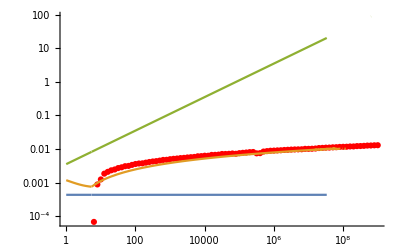

## compton

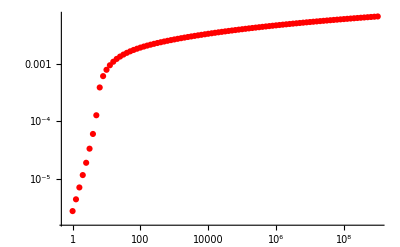

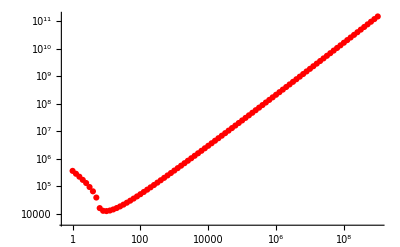

```mathematica
MwdVal=1.37;
numsubs={α->αval,Z->0,ne->nElectronMeV[MwdVal],M->0,m->mElectron,λTF->λThomasFermi[MwdVal]};
ϵvals=Table[10^(.1x),{x,0,90}];
expr=1/v 1/2 HoldIntegrate[Sin[ψ]dNdtLabCompton ωtrans HeavisideTheta[ωtrans-(ϵf-ϵe)],{ϕ,0,2π},{ψ,0,π},{ϵe,0,ϵf},{cosθ,-1,1},MaxPoints->100000,MinRecursion->5]//.numsubs;
comptonHighDensityResults=Quiet@Monitor[Table[{ϵ,expr}/.HoldIntegrate->NIntegrate,{ϵ,ϵvals}],ϵ];
ListLogLogPlot[comptonHighDensityResults,PlotRange->All,PlotStyle->Red]
ListLogLogPlot[{#[[1]],(#[[1]])/(#[[2]])}&/@comptonHighDensityResults,PlotRange->All,PlotStyle->Red]
```

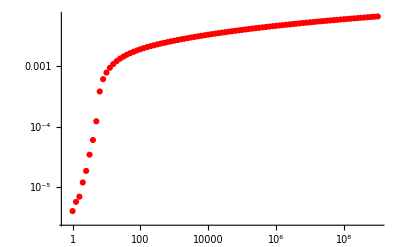
```mathematica
comptonguess=2π(ne α^2)/m;
Show[-Graphics-,LogLogPlot[Evaluate[{
comptonguess/.numsubs}],{ϵ,1000,10^9},PlotStyle->Orange]]
```

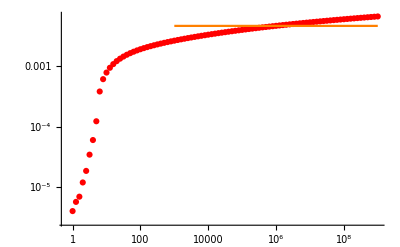

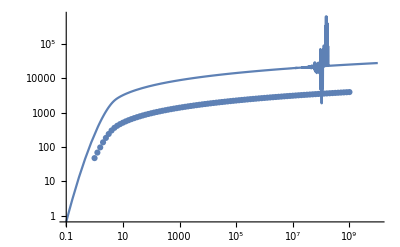
```mathematica
Show[-Graphics-,LogLogPlot[5*10^5*dEdxCompton[ϵ,1.37],{ϵ,1,10^9},PlotStyle->Red],PlotRange->All]
```

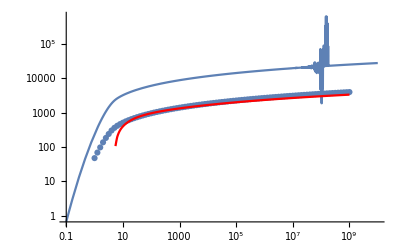

## Making dEdx interpolations

```mathematica
dEdxCoulombPionsOffElectrons[ϵ_,1.37]=Interpolation[pionHighDensityResults][ϵ];
dEdxCoulombProtonsOffElectrons[ϵ_,1.37]=Interpolation[protonHighDensityResults][ϵ];
dEdxCoulombIonsOffElectrons[ϵ_,1.37]=Interpolation[ionHighDensityResults][ϵ];
dEdxCoulombElectronsOffElectrons[ϵ_,1.37]=Interpolation[electronHighDensityResults][ϵ];
dEdxCompton[ϵ_,1.37]=Interpolation[comptonHighDensityResults][ϵ];
```

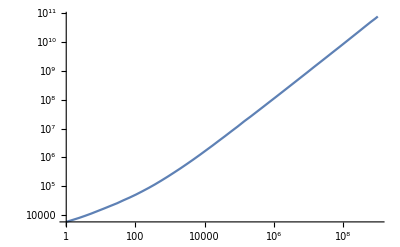

```mathematica
dEdxCoulombPionsOffElectrons[ϵ_,1.37]=Interpolation[pionHighDensityResults][ϵ];
LogLogPlot[ϵ/dEdxCoulombPionsOffElectrons[ϵ,1.37],{ϵ,1,10^9}]
```

Stopping Power Results, low density

## pion

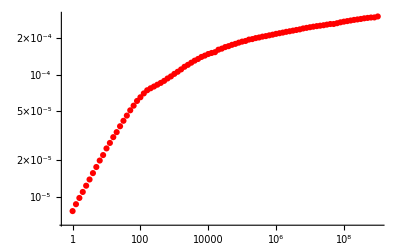

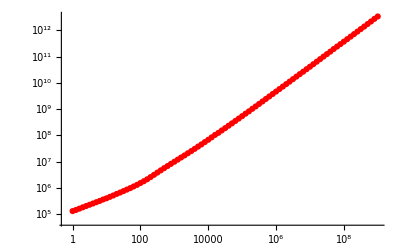

```mathematica
MwdVal=0.85;
numsubs={α->αval,Z->1,ne->nElectronMeV[MwdVal],M->mPion,m->mElectron,λTF->λThomasFermi[MwdVal]};
ϵvals=Table[10^(.1x),{x,0,90}];
expr=1/v 1/2 HoldIntegrate[Sin[ψ]dNdtLabMassivePhoton ωtrans HeavisideTheta[ωtrans-(ϵf-ϵe)],{ϕ,0,2π},{ψ,0,π},{ϵe,0,ϵf},{cosθ,-1,1},MaxPoints->100000,MinRecursion->5]//.numsubs;
pionLowDensityResults=Quiet@Monitor[Table[{ϵ,expr}/.HoldIntegrate->NIntegrate,{ϵ,ϵvals}],ϵ];
ListLogLogPlot[pionLowDensityResults,PlotRange->All,PlotStyle->Red]
ListLogLogPlot[{#[[1]],(#[[1]])/(#[[2]])}&/@pionLowDensityResults,PlotRange->All,PlotStyle->Red]
```

```mathematica
ryan=(2π Z^2 α^2 ne)/(m+Ef)(Integrate[1/ω(1-(1+(ω(ω-2Ef))/Pf^2)),{ω,0,Min[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}]+Integrate[1/ω,{ω,Min[ωkin,Ef],Max[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}])//FullSimplify
```

(ne π Z^2 α^2 (2 Pf^2 Log[Max[Ef,ωkin]/Min[Ef,ωkin]]+4 Ef Min[Ef,ωkin]-Min[Ef,ωkin]^2))/((Ef+m) Pf^2)

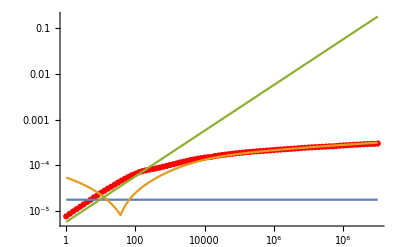

```mathematica
Show[ListLogLogPlot[pionLowDensityResults,PlotRange->All,PlotStyle->Red],LogLogPlot[Evaluate[{
(2π Z^2 α^2 ne)/ϵf/.numsubs,
3/2 ryan//.{Ef->ϵf,Pf->pf,ωkin->(2m vel^2 γ^2)/(1+2γ m/M+(m/M)^2),γ->(1-vel^2)^(-1/2),vel->(√(EE^2-M^2))/EE,EE->ϵ+M}/.numsubs,
1/4*3/2 ne (Z^2 α^2)/pf √((2ϵ)/M)*Ia/.{Ia->75}/.numsubs}],{ϵ,1,10^9}], PlotRange->All]
```

## proton

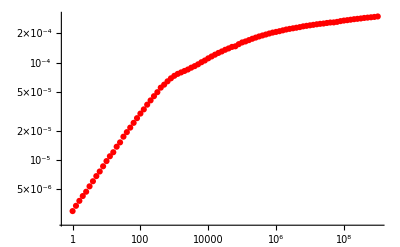

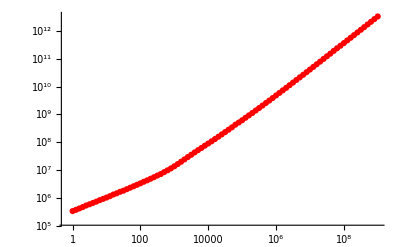

```mathematica
MwdVal=0.85;
numsubs={α->αval,Z->1,ne->nElectronMeV[MwdVal],M->mProton,m->mElectron,λTF->λThomasFermi[MwdVal]};
ϵvals=Table[10^(.1x),{x,0,90}];
expr=1/v 1/2 HoldIntegrate[Sin[ψ]dNdtLabMassivePhoton ωtrans HeavisideTheta[ωtrans-(ϵf-ϵe)],{ϕ,0,2π},{ψ,0,π},{ϵe,0,ϵf},{cosθ,-1,1},MaxPoints->100000,MinRecursion->5]//.numsubs;
protonLowDensityResults=Quiet@Monitor[Table[{ϵ,expr}/.HoldIntegrate->NIntegrate,{ϵ,ϵvals}],ϵ];
ListLogLogPlot[protonLowDensityResults,PlotRange->All,PlotStyle->Red]
ListLogLogPlot[{#[[1]],(#[[1]])/(#[[2]])}&/@protonLowDensityResults,PlotRange->All,PlotStyle->Red]
```

```mathematica
ryan=(2π Z^2 α^2 ne)/(m+Ef)(Integrate[1/ω(1-(1+(ω(ω-2Ef))/Pf^2)),{ω,0,Min[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}]+Integrate[1/ω,{ω,Min[ωkin,Ef],Max[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}])//FullSimplify
```

(ne π Z^2 α^2 (2 Pf^2 Log[Max[Ef,ωkin]/Min[Ef,ωkin]]+4 Ef Min[Ef,ωkin]-Min[Ef,ωkin]^2))/((Ef+m) Pf^2)

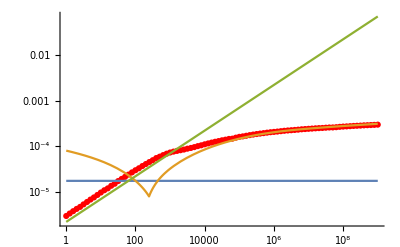

```mathematica
Show[ListLogLogPlot[protonLowDensityResults,PlotRange->All,PlotStyle->Red],LogLogPlot[Evaluate[{
(2π Z^2 α^2 ne)/ϵf/.numsubs,
3/2 ryan//.{Ef->ϵf,Pf->pf,ωkin->(2m vel^2 γ^2)/(1+2γ m/M+(m/M)^2),γ->(1-vel^2)^(-1/2),vel->(√(EE^2-M^2))/EE,EE->ϵ+M}/.numsubs,
1/4*3/2 ne (Z^2 α^2)/pf √((2ϵ)/M)*Ia/.{Ia->75}/.numsubs}],{ϵ,1,10^9}], PlotRange->All]
```

## ion

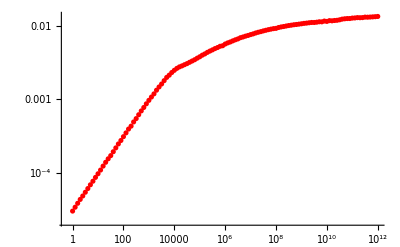

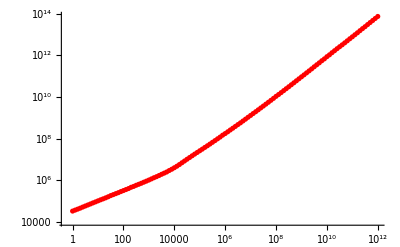

```mathematica
MwdVal=0.85;
numsubs={α->αval,Z->ZCarbon,ne->nElectronMeV[MwdVal],M->mCarbon,m->mElectron,λTF->λThomasFermi[MwdVal]};
ϵvalsLowϵ=Table[10^(.1x),{x,0,30}];
ϵvals=Table[10^(.1x),{x,31,120}];
expr1=1/v 1/2 HoldIntegrate[Sin[ψ]dNdtLabMassivePhoton ωtrans HeavisideTheta[ωtrans-(ϵf-ϵe)],{ϕ,0,2π},{ψ,0,π},{ϵe,0,ϵf},{cosθ,-1,1},MaxPoints->100000,MinRecursion->5]//.numsubs;
expr2=1/v 1/2 HoldIntegrate[Sin[ψ]dNdtLabMassivePhoton ωtrans HeavisideTheta[ωtrans-(ϵf-ϵe)],{ϕ,0,2π},{ψ,0,π},{ϵe,0,ϵf},{cosθ,-1,1},MaxPoints->100000,MinRecursion->5]//.numsubs;
ionLowDensityResultsLowϵ=Quiet@Monitor[Table[{ϵ,expr1}/.HoldIntegrate->NIntegrate,{ϵ,ϵvalsLowϵ}],ϵ];
ionLowDensityResults=ionLowDensityResultsLowϵ∪Quiet@Monitor[Table[{ϵ,expr2}/.HoldIntegrate->NIntegrate,{ϵ,ϵvals}],ϵ];
ListLogLogPlot[ionLowDensityResults,PlotRange->All,PlotStyle->Red]
ListLogLogPlot[{#[[1]],(#[[1]])/(#[[2]])}&/@ionLowDensityResults,PlotRange->All,PlotStyle->Red]
```

```mathematica
ryan=(2π Z^2 α^2 ne)/(m+Ef)(Integrate[1/ω(1-(1+(ω(ω-2Ef))/Pf^2)),{ω,0,Min[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}]+Integrate[1/ω,{ω,Min[ωkin,Ef],Max[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}])//FullSimplify
```

(ne π Z^2 α^2 (2 Pf^2 Log[Max[Ef,ωkin]/Min[Ef,ωkin]]+4 Ef Min[Ef,ωkin]-Min[Ef,ωkin]^2))/((Ef+m) Pf^2)

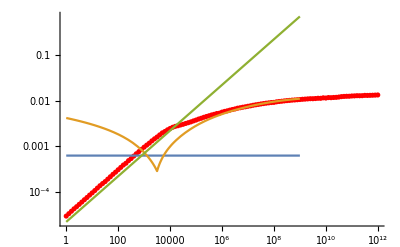

```mathematica
Show[ListLogLogPlot[ionLowDensityResults,PlotRange->All,PlotStyle->Red],LogLogPlot[Evaluate[{
(2π Z^2 α^2 ne)/ϵf/.numsubs,
3/2 ryan//.{Ef->ϵf,Pf->pf,ωkin->(2m vel^2 γ^2)/(1+2γ m/M+(m/M)^2),γ->(1-vel^2)^(-1/2),vel->(√(EE^2-M^2))/EE,EE->ϵ+M}/.numsubs,
1/4*3/2 ne (Z^2 α^2)/pf √((2ϵ)/M)*Ia/.{Ia->75}/.numsubs}],{ϵ,1,10^9}], PlotRange->All]
```

## electron

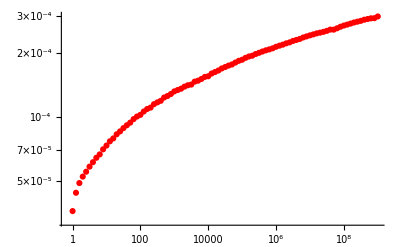

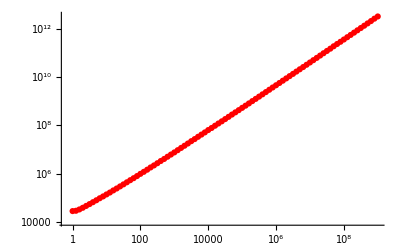

```mathematica
MwdVal=0.85;
numsubs={α->αval,Z->1,ne->nElectronMeV[MwdVal],M->mElectron,m->mElectron,λTF->λThomasFermi[MwdVal]};
ϵvals=Table[10^(.1x),{x,0,90}];
expr=1/v 1/2 HoldIntegrate[Sin[ψ]dNdtLabMassivePhotonElectron ωtrans HeavisideTheta[ωtrans-(ϵf-ϵe)]HeavisideTheta[(ϵ-ωtrans)-ϵf],{ϕ,0,2π},{ψ,0,π},{ϵe,0,ϵf},{cosθ,-1,1},MaxPoints->100000,MinRecursion->5]//.numsubs;
electronLowDensityResults=Quiet@Monitor[Table[{ϵ,expr}/.HoldIntegrate->NIntegrate,{ϵ,ϵvals}],ϵ];
ListLogLogPlot[electronLowDensityResults,PlotRange->All,PlotStyle->Red]
ListLogLogPlot[{#[[1]],(#[[1]])/(#[[2]])}&/@electronLowDensityResults,PlotRange->All,PlotStyle->Red]
```

```mathematica
ryan=(2π Z^2 α^2 ne)/(m+Ef)(Integrate[1/ω(1-(1+(ω(ω-2Ef))/Pf^2)),{ω,0,Min[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}]+Integrate[1/ω,{ω,Min[ωkin,Ef],Max[ωkin,Ef]},Assumptions->{Ef>0,ωkin>0,m>0}])//FullSimplify
```

(ne π Z^2 α^2 (2 Pf^2 Log[Max[Ef,ωkin]/Min[Ef,ωkin]]+4 Ef Min[Ef,ωkin]-Min[Ef,ωkin]^2))/((Ef+m) Pf^2)

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

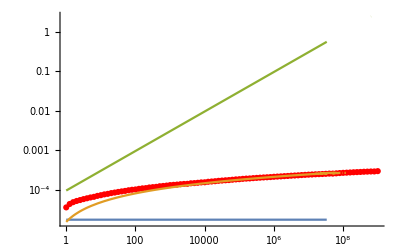

```mathematica
Show[ListLogLogPlot[electronLowDensityResults,PlotRange->All,PlotStyle->Red],LogLogPlot[Evaluate[{
(2π Z^2 α^2 ne)/ϵf/.numsubs,
3/2 ryan//.{Ef->ϵf,Pf->pf,ωkin->(2m vel^2 γ^2)/(1+2γ m/M+(m/M)^2),γ->(1-vel^2)^(-1/2),vel->(√(EE^2-M^2))/EE,EE->ϵ+M}/.numsubs,
1/4*3/2 ne (Z^2 α^2)/pf √((2ϵ)/M)*Ia/.{Ia->75}/.numsubs}],{ϵ,1,10^9}], PlotRange->All]
```

## compton

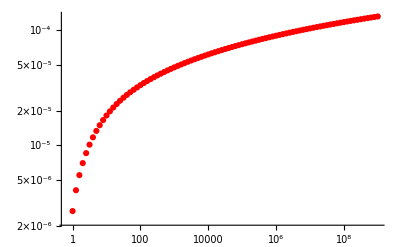

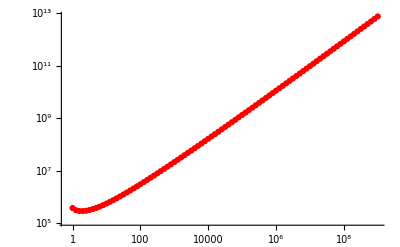

```mathematica
MwdVal=0.85;
numsubs={α->αval,Z->0,ne->nElectronMeV[MwdVal],M->0,m->mElectron,λTF->λThomasFermi[MwdVal]};
ϵvals=Table[10^(.1x),{x,0,90}];
expr=1/v 1/2 HoldIntegrate[Sin[ψ]dNdtLabCompton ωtrans HeavisideTheta[ωtrans-(ϵf-ϵe)],{ϕ,0,2π},{ψ,0,π},{ϵe,0,ϵf},{cosθ,-1,1},MaxPoints->100000,MinRecursion->5]//.numsubs;
comptonLowDensityResults=Quiet@Monitor[Table[{ϵ,expr}/.HoldIntegrate->NIntegrate,{ϵ,ϵvals}],ϵ];
ListLogLogPlot[comptonLowDensityResults,PlotRange->All,PlotStyle->Red]
ListLogLogPlot[{#[[1]],(#[[1]])/(#[[2]])}&/@comptonLowDensityResults,PlotRange->All,PlotStyle->Red]
```

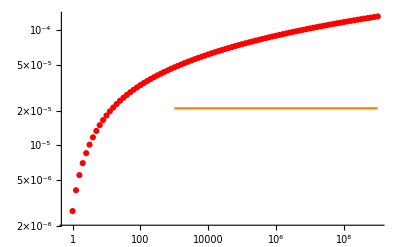

```mathematica
comptonguess=2π(ne α^2)/m;
Show[ListLogLogPlot[comptonLowDensityResults,PlotRange->All,PlotStyle->Red],LogLogPlot[Evaluate[{
comptonguess/.numsubs}],{ϵ,1000,10^9},PlotStyle->Orange]]
```

## Making dEdx interpolations

```mathematica
dEdxCoulombPionsOffElectrons[ϵ_,0.85]=Interpolation[pionLowDensityResults][ϵ];
dEdxCoulombProtonsOffElectrons[ϵ_,0.85]=Interpolation[protonLowDensityResults][ϵ];
dEdxCoulombIonsOffElectrons[ϵ_,0.85]=Interpolation[ionLowDensityResults][ϵ];
dEdxCoulombElectronsOffElectrons[ϵ_,0.85]=Interpolation[electronLowDensityResults][ϵ];
dEdxCompton[ϵ_,0.85]=Interpolation[comptonLowDensityResults][ϵ];
```

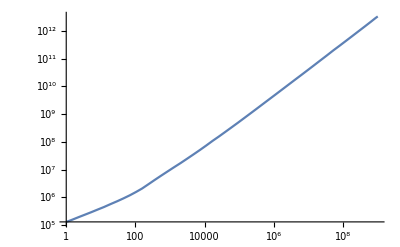

```mathematica
dEdxCoulombPionsOffElectrons[ϵ_,0.85]=Interpolation[pionLowDensityResults][ϵ];
LogLogPlot[ϵ/dEdxCoulombPionsOffElectrons[ϵ,0.85],{ϵ,1,10^9}]
```

Saving and loading interpolations

```mathematica
Directory[]
(*DumpSave["StoppingPowerInterpolations.mx",
{dEdxCoulombPionsOffElectrons,
dEdxCoulombProtonsOffElectrons,
dEdxCoulombIonsOffElectrons,
dEdxCoulombElectronsOffElectrons,
dEdxCompton}]*) (* commented to avoid accidentally overwriting existing results *)
```

/Users/priggins/Dropbox/Berkeley-current/Research/WhiteDwarfParticleDetector/Qballs

Run the following to avoid having to rerun everything all over again.

```mathematica
<<"StoppingPowerInterpolations.mx"
```

```mathematica
dEdxCoulombIonsOffElectronsLowEnergy[ϵ_,Mwd_]:=ne (Z^2 α^2)/ϵf(√(2M ϵ))/M*Ia/.{Ia->10}/.{α->αval,Z->ZCarbon,ne->nElectronMeV[Mwd],M->mCarbon,m->mElectron,λTF->λThomasFermi[Mwd]};
dEdxCoulombIonsOffElectronsHighEnergy[ϵ_,Mwd_]:=ne (2π α^2 Z^2)/Ef G[ωKIN/Ef]//.{Ef->ϵf,Pf->pf,ωKIN->(2m vel^2 γ^2)/(1+2γ m/M+(m/M)^2),γ->(1-vel^2)^(-1/2),vel->(√(EE^2-M^2))/EE,EE->ϵ+M,G->Function[x,Piecewise[{{x^3/3-3/2 x^2+3x,x<1},{11/6+Log[x],x>1}}]]}/.{α->αval,Z->ZCarbon,ne->nElectronMeV[Mwd],M->mCarbon,m->mElectron,λTF->λThomasFermi[Mwd]};
```

## Coulomb (off electrons): limiting cases

Limiting cases

```mathematica
(* valid for m >> p ~ √(2 m ϵ), for incident mass m *)
dEdxCoulombOffElectronsLowEnergy[ϵ_,Mwd_,mIncident_,Zincident_]:=ne (Z^2 α^2)/ϵf(√(2M ϵ))/M*Ia/.{Ia->10}/.{α->αval,Z->Zincident,ne->nElectronMeV[Mwd],M->mIncident,m->mElectron,λTF->λThomasFermi[Mwd],ϵf->EFermiMeV[Mwd]};

(* valid for m << p ~ ϵ, for incident mass m *)
dEdxCoulombOffElectronsHighEnergy[ϵ_,Mwd_,mIncident_,Zincident_]:=ne (2π α^2 Z^2)/Ef G[ωKIN/Ef]//.{Ef->ϵf,Pf->pf,ωKIN->(2m vel^2 γ^2)/(1+2γ m/M+(m/M)^2),γ->(1-vel^2)^(-1/2),vel->(√(EE^2-M^2))/EE,EE->ϵ+M,G->Function[x,Piecewise[{{x^3/3-3/2 x^2+3x,x<1},{11/6+Log[x],x>1}}]]}/.{α->αval,Z->Zincident,ne->nElectronMeV[Mwd],M->mIncident,m->mElectron,λTF->λThomasFermi[Mwd],ϵf->EFermiMeV[Mwd]};

dEdxCoulombOffElectronsMidEnergyInterpolation[ϵ_,Mwd_,mIncident_,Zincident_]:=Module[{thresholdEnergy1,thresholdEnergy2,interpolationPoint1,interpolationPoint2,f1,f2,E1,E2},
thresholdEnergy1=0.1*√(2 mIncident^2); (* upper limit of validity for non-rel *)
thresholdEnergy2=10*mIncident; (* lower limit of validity for rel *)
interpolationPoint1=dEdxCoulombOffElectronsLowEnergy[thresholdEnergy1,Mwd,mIncident,Zincident];
interpolationPoint2=dEdxCoulombOffElectronsHighEnergy[thresholdEnergy2,Mwd,mIncident,Zincident];

α2val=Log[f1/f2]/(Log[E1]-Log[E2])/.{E1->thresholdEnergy1,E2->thresholdEnergy2,f1->interpolationPoint1,f2->interpolationPoint2};
α1val=f1*E1^-α2val/.{E1->thresholdEnergy1,E2->thresholdEnergy2,f1->interpolationPoint1,f2->interpolationPoint2};
Return[α1val ϵ^α2val];
];

dEdxCoulombOffElectronsFull[ϵ_,Mwd_,mIncident_,Zincident_]:=Module[{thresholdEnergy1,thresholdEnergy2},
thresholdEnergy1=0.1*√(2 mIncident^2); (* upper limit of validity for non-rel *)
thresholdEnergy2=10*mIncident; (* lower limit of validity for rel *)
Return@Piecewise[{
{dEdxCoulombOffElectronsLowEnergy[ϵ,Mwd,mIncident,Zincident],ϵ<thresholdEnergy1},
{dEdxCoulombOffElectronsHighEnergy[ϵ,Mwd,mIncident,Zincident],ϵ>thresholdEnergy2},
{dEdxCoulombOffElectronsMidEnergyInterpolation[ϵ,Mwd,mIncident,Zincident],thresholdEnergy1<ϵ<thresholdEnergy2}
}]
];
```

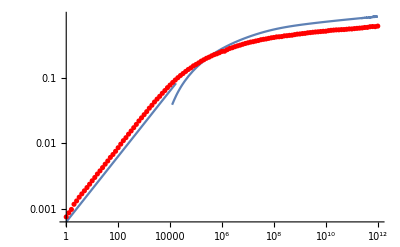

```mathematica
MwdVal=1.37;
incidentMass=mCarbon;
incidentCharge=ZCarbon;
Show[
LogLogPlot[2dEdxCoulombOffElectronsLowEnergy[ϵ,MwdVal,incidentMass,incidentCharge],{ϵ,1,√(2 incidentMass^2)}],
LogLogPlot[2dEdxCoulombOffElectronsHighEnergy[ϵ,MwdVal,incidentMass,incidentCharge],{ϵ,incidentMass,10^12}],
-Graphics-,
PlotRange->All]
```

```mathematica
Solve[{α1 E1^α2==f1,α1 E2^α2==f2},{α1,α2}]
```

```mathematica
{{α1->ConditionalExpression[E1^(-(2 ⅈ π C[1]+Log[f1/f2])/(Log[E1]-Log[E2])) f1,C[1]∈Integers],α2->ConditionalExpression[Log[f1/f2]/(Log[E1]-Log[E2]),C[1]∈Integers]}}
```

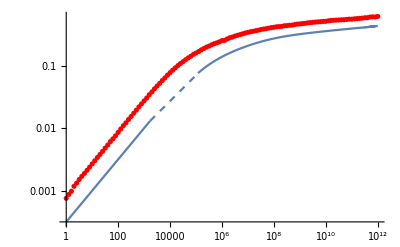

```mathematica
MwdVal=1.37;
incidentMass=mCarbon;
incidentCharge=ZCarbon;
thresholdEnergy1=0.1*√(2 incidentMass^2);
thresholdEnergy2=10*incidentMass;
interpolationPoint1=dEdxCoulombOffElectronsLowEnergy[thresholdEnergy1,MwdVal,incidentMass,incidentCharge];
interpolationPoint2=dEdxCoulombOffElectronsHighEnergy[thresholdEnergy2,MwdVal,incidentMass,incidentCharge];

α2val=Log[f1/f2]/(Log[E1]-Log[E2])/.{E1->thresholdEnergy1,E2->thresholdEnergy2,f1->interpolationPoint1,f2->interpolationPoint2};
α1val=f1*E1^-α2val/.{E1->thresholdEnergy1,E2->thresholdEnergy2,f1->interpolationPoint1,f2->interpolationPoint2};

Show[
LogLogPlot[dEdxCoulombOffElectronsLowEnergy[ϵ,MwdVal,incidentMass,incidentCharge],{ϵ,1,thresholdEnergy1}],
LogLogPlot[dEdxCoulombOffElectronsHighEnergy[ϵ,MwdVal,incidentMass,incidentCharge],{ϵ,thresholdEnergy2,10^12}],
LogLogPlot[α1val ϵ^α2val,{ϵ,thresholdEnergy1,thresholdEnergy2},PlotStyle->Dashed],
-Graphics-,
PlotRange->All]
```

## Checking against numerics

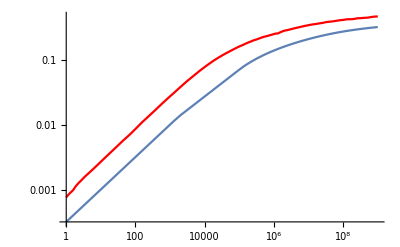

```mathematica
MwdVal=1.37;
incidentMass=mCarbon;
incidentCharge=ZCarbon;
Show[LogLogPlot[dEdxCoulombOffElectronsFull[ϵ,MwdVal,incidentMass,incidentCharge],{ϵ,1,10^9}],LogLogPlot[dEdxCoulombIonsOffElectrons[ϵ,MwdVal],{ϵ,1,10^9},PlotStyle->Red],PlotRange->All]
```

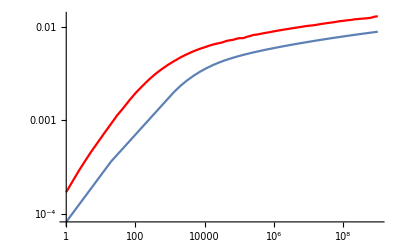

```mathematica
MwdVal=1.37;
incidentMass=mPion;
incidentCharge=1;
Show[LogLogPlot[dEdxCoulombOffElectronsFull[ϵ,MwdVal,incidentMass,incidentCharge],{ϵ,1,10^9}],LogLogPlot[dEdxCoulombPionsOffElectrons[ϵ,MwdVal],{ϵ,1,10^9},PlotStyle->Red],PlotRange->All]
```

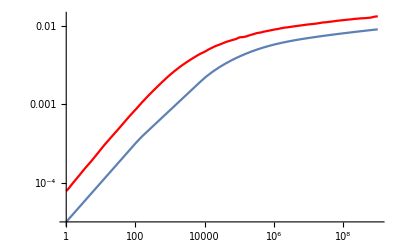

```mathematica
MwdVal=1.37;
incidentMass=mProton;
incidentCharge=1;
Show[LogLogPlot[dEdxCoulombOffElectronsFull[ϵ,MwdVal,incidentMass,incidentCharge],{ϵ,1,10^9}],LogLogPlot[dEdxCoulombProtonsOffElectrons[ϵ,MwdVal],{ϵ,1,10^9},PlotStyle->Red],PlotRange->All]
```

## Old (bad) coulomb and compton off electrons

Coulomb collisions of hadrons off electrons

The derivation for coulomb collisions off electrons is the same as hadrons off ions, except with different target number density.

```mathematica
dEdxCoulombHadronsOffElectrons[ϵ_?NumericQ,m_,Mwd_]:=NIntegrateTEMP[dσdωCoulomb[ω]ne ω,{ω,ωSCR,ωKIN}]//.
{ωSCR->ωscr[ϵ,m,M,Mwd],ωKIN->ωkin[ϵ,m,M],
M->mElectron,Z->-1(*electron targets*),ne->nElectronEffective[ω,Mwd],
α->αval,Ef->EFermiMeV[Mwd],β->√(1-γ^-2),γ->ϵ/m+1}/.NIntegrateTEMP->NIntegrate;
```

### Pions off electrons

```mathematica
nIonMeV[1.37]
```

1.15996

```mathematica
nElectronMeV[1.3735]
```

8.06291

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffElectrons[ϵ,mPion,1.37],{ϵ,.1,10^7}]
```

-Graphics-

Comparing to Vijay’s results, mine cut off a factor of 10 sooner in energy, but otherwise match well.

```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

-Graphics-

#### Low densities

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffElectrons[ϵ,mPion,0.85],{ϵ,.1,10^7}],-Graphics-,PlotRange->All]
```

### Protons off electrons

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffElectrons[ϵ,mProton,1.37],{ϵ,.1,10^7}]
```

-Graphics-

Comparing to Vijay’s results, mine cut off a factor of 10 sooner in energy, but otherwise match well.

```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

-Graphics-

### Low densities

Comparing to Vijay’s results, mine cut off a factor of 10 sooner in energy, but otherwise match well.

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombHadronsOffElectrons[ϵ,mProton,0.85],{ϵ,.1,10^7}],-Graphics-,PlotRange->All]
```

-Graphics-

Coulomb collisions of electrons off electrons

The derivation for coulomb collisions off electrons is the same as electrons off ions, except with different target number density. ω_kin also happens to be a factor of 2 smaller, presumably because of indistinguishability.

```mathematica
dEdxCoulombElectronsOffElectrons[ϵ_?NumericQ,Mwd_]:=NIntegrateTEMP[dσdωCoulomb[ω]ne ω,{ω,ωSCR,ωKIN}]//.
{ωSCR->ωscr[ϵ,m,M,Mwd],ωKIN->ωkin[ϵ,m,M]/2,
m->mElectron,M->mElectron,Z->-1(*electron targets*),ne->nElectronEffective[ω,Mwd],
α->αval,Ef->EFermiMeV[Mwd],β->√(1-γ^-2),γ->ϵ/m+1}/.NIntegrateTEMP->NIntegrate;
```

### Electrons off electrons

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombElectronsOffElectrons[ϵ,1.37],{ϵ,8,10^7}]
```

-Graphics-

Comparing to Vijay’s results, we see they match pretty well

```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

-Graphics-

#### Low densities

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*dEdxCoulombElectronsOffElectrons[ϵ,1.37],{ϵ,8,10^7}]
```

-Graphics-

Comparing to Vijay’s results, we see they match pretty well

```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

-Graphics-

Compton and inverse compton scattering

## Compton scattering with Pauli-Blocking

### Electrons

The differential cross section for Compton scattering is

```mathematica
dσdΩCompton[cosθ_]:=α^2/me^2 P^2/2(P+1/P-Sin[θ]^2)/.P->1/(1+k/me(1-Cos[θ]))//.{Sin[θ]^2->1-Cos[θ]^2,Cos[θ]->cosθ}//FullSimplify;
```

Integrating out the azimuthal dependence,

```mathematica
dσdcosθCompton[cosθ_]:=2π*dσdΩCompton[cosθ];
dσdcosθCompton[cosθ]
```

((cosθ^2+(k-cosθ k)/me+me/(k-cosθ k+me)) π α^2)/(k-cosθ k+me)^2

The energy transferred by a photon of energy k scattering at angle θ off an electron is

```mathematica
EtransferredCompton[cosθ_]:=k-k/(1+(k (1-cosθ))/me);
```

This exceeds the Fermi energy for angles

```mathematica
Solve[EtransferredCompton[cosθ]==Ef,cosθ]//FullSimplify
```

{{cosθ→1+(Ef me)/((Ef-k) k)}}

```mathematica
Plot[Evaluate[1+(Ef me)/((Ef-k) k)/.{Ef->EFermiMeV[1.37],me->mElectron}],{k,1,20}]
```

-Graphics-

and smaller (and negative) values of cosθ.

Note the effective electron density is reduced in the Fermi sea. (see nElectronEffective defined along with the electron number density in the White Dwarf parameters section above.)

So the Compton stopping power on electrons is

```mathematica
Plot[nElectronEffective[ω,1.37],{ω,0,10}]
```

-Graphics-

```mathematica
dEdxComptonEst[ϵ_?NumericQ,Mwd_?NumericQ]:=Int[dσdcosθCompton[cosθ]n ω,{cosθ,-1,1}]//.{n->nElectronEffective[ω,Mwd],ω->EtransferredCompton[cosθ],Ef->EFermiMeV[Mwd],k->ϵ,me->mElectron,α->αval}/.Int->NIntegrate;
```

```mathematica
LogLogPlot[ConvertMeV2ToMeVPerTrigger*Quiet@dEdxComptonEst[ϵ,1.37],{ϵ,.1,10^10},PlotRange->All]
```

$Aborted

```mathematica
nElectronMeV[1.37]
```

6.95976

This matches Vijay’s result excellently.

```mathematica
Show[LogLogPlot[dEdxCompton[ϵ,MwdVal],{ϵ,1,10^9},PlotStyle->Red],LogLogPlot[Quiet@dEdxComptonEst[ϵ,1.37],{ϵ,.1,10^9},PlotRange->All]]
```

-Graphics-

```mathematica
Show[
LogLogPlot[Evaluate[20(ne α^2)/me(1-me/ϵ)/.{ne->7,α->αval,me->mElectron}],{ϵ,1,10^2},PlotStyle->Green],
LogLogPlot[Evaluate[20(ne α^2)/me(1-me/ϵ)/.{ne->7,α->αval,me->mElectron}],{ϵ,1,10^9},PlotStyle->Green],-Graphics-,PlotRange->All]
```

-Graphics-

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

#### Low densities

```mathematica
nElectronMeV[0.85]
```

0.0311932

For a low-mass white dwarf, comparing to Vijay’s result, this again matches excellently

```mathematica
Show[LogLogPlot[ConvertMeV2ToMeVPerTrigger*Quiet@dEdxCompton[ϵ,0.85],{ϵ,.1,10^15},PlotRange->All],-Graphics-]
```

-Graphics-

### Protons

even more negligible.

## Inverse compton

negligible, because the photon number density is so much smaller than the electron number density.

# Lambda plots

Everything together

### High density

```mathematica
MwdVal=1.37;
triggerSizeNormalization=10^-5.;
curves={
{triggerSizeVersusMass[MwdVal]/triggerSizeNormalization ConvertMeV2ToMeVPerTrigger,"Trigger Size λ_T",{Thick,Black}},
{ϵ/dEdxNonelastic[ϵ,MwdVal],"Nuclear Inelastic",Purple},
{ϵ/dEdxCoulombElectronsOffElectrons[ϵ,MwdVal],"Coulomb, electron-electron",Lighter@Lighter@Orange},
{ϵ/dEdxCoulombPionsOffElectrons[ϵ,MwdVal],"Coulomb, pion-electron",Orange},
{ϵ/dEdxCoulombProtonsOffElectrons[ϵ,MwdVal],"Coulomb, proton-electron",Darker[Orange]},
{ϵ/dEdxBremElectronSimple[ϵ,MwdVal],"Pair production",{LightGreen,Thick}},
{ϵ/dEdxBremElectronSimple[ϵ,MwdVal],"Bremsstrahlung, electron",Green},
(*{ϵ/dEdxBremPion[ϵ,MwdVal],"Bremsstrahlung, pion",Darker[Green]},*)
{ϵ/dEdxDirectPP[ϵ,MwdVal],"Direct pair production",Yellow},
{ϵ/dEdxCompton[ϵ,MwdVal],"Compton, γ-electron",Red},
{ϵ/dEdxPhotonuclear[ϵ,MwdVal],"Photonuclear",Pink},
{ϵ/dEdxElectronuclear[ϵ,MwdVal],"Electronuclear",Magenta},
{ϵ/dEdxCoulombElectronsOffIons[ϵ,MwdVal],"Coulomb, electron-ion",Lighter@Lighter@Blue},
{ϵ/dEdxCoulombHadronsOffIons[ϵ,mPion,MwdVal],"Coulomb, pion-ion",Blue},
{ϵ/dEdxCoulombHadronsOffIons[ϵ,mProton,MwdVal],"Coulomb, proton-ion",Darker[Blue]},
{(ϵ/dEdxElasticPion[ϵ,MwdVal])/√BounceCount/.{BounceCount->100},"Elastic pion",Cyan},
{(ϵ/dEdxElasticNucleon[ϵ,MwdVal])/√BounceCount/.{BounceCount->10},"Elastic nucleon",Darker[Cyan]},
{ϵ/dEdxCoulombIonsOffElectrons[ϵ,MwdVal],"Coulomb, ion-electron",Brown}
};
Quiet@LogLogPlot[Evaluate[(#[[1]])/ConvertMeV2ToMeVPerTrigger&/@curves],{ϵ,1,10^8},
PlotLegends->(#[[2]]&/@curves),
PlotStyle->(#[[3]]&/@curves),
PlotRange->{10^-3,10^3},
Frame->True,FrameLabel->{"Energy (MeV)","λ (10^-5 cm)"},PlotLabel->"All stopping powers, high-density (M_WD=1.37M_☉)",
ImageSize->Large]
```

-Graphics-

### Low density

```mathematica
MwdVal=0.85;
triggerSizeNormalization=10^-5.;
curves={
{triggerSizeVersusMass[MwdVal]/triggerSizeNormalization ConvertMeV2ToMeVPerTrigger,"Trigger Size λ_T",{Thick,Black}},
{ϵ/dEdxNonelastic[ϵ,MwdVal],"Nuclear Inelastic",Purple},
{ϵ/dEdxCoulombElectronsOffElectrons[ϵ,MwdVal],"Coulomb, electron-electron",Lighter@Lighter@Orange},
{ϵ/dEdxCoulombPionsOffElectrons[ϵ,MwdVal],"Coulomb, pion-electron",Orange},
{ϵ/dEdxCoulombProtonsOffElectrons[ϵ,MwdVal],"Coulomb, proton-electron",Darker[Orange]},
{ϵ/dEdxBremElectronSimple[ϵ,MwdVal],"Pair production",{LightGreen,Thick}},
{ϵ/dEdxBremElectronSimple[ϵ,MwdVal],"Bremsstrahlung, electron",Green},
(*{ϵ/dEdxBremPion[ϵ,MwdVal],"Bremsstrahlung, pion",Darker[Green]},*)
{ϵ/dEdxDirectPP[ϵ,MwdVal],"Direct pair production",Yellow},
{ϵ/dEdxCompton[ϵ,MwdVal],"Compton, γ-electron",Red},
{ϵ/dEdxPhotonuclear[ϵ,MwdVal],"Photonuclear",Pink},
{ϵ/dEdxElectronuclear[ϵ,MwdVal],"Electronuclear",Magenta},
{ϵ/dEdxCoulombElectronsOffIons[ϵ,MwdVal],"Coulomb, electron-ion",Lighter@Lighter@Blue},
{ϵ/dEdxCoulombHadronsOffIons[ϵ,mPion,MwdVal],"Coulomb, pion-ion",Blue},
{ϵ/dEdxCoulombHadronsOffIons[ϵ,mProton,MwdVal],"Coulomb, proton-ion",Darker[Blue]},
{(ϵ/dEdxElasticPion[ϵ,MwdVal])/√BounceCount/.{BounceCount->100},"Elastic pion",Cyan},
{(ϵ/dEdxElasticNucleon[ϵ,MwdVal])/√BounceCount/.{BounceCount->10},"Elastic nucleon",Darker[Cyan]},
{ϵ/dEdxCoulombIonsOffElectrons[ϵ,MwdVal],"Coulomb, ion-electron",Brown}
};
Quiet@LogLogPlot[Evaluate[(#[[1]])/ConvertMeV2ToMeVPerTrigger&/@curves],{ϵ,1,10^7},
PlotLegends->(#[[2]]&/@curves),
PlotStyle->(#[[3]]&/@curves),
PlotRange->{10^-1,10^5},
Frame->True,FrameLabel->{"Energy (MeV)","λ (10^-5 cm)"},PlotLabel->"All stopping powers, low-density (M_WD=0.85M_☉)",
ImageSize->Large]
```

-Graphics-

```mathematica
EFermiMeV[0.85]
```

0.973853

Trigger size, eγ, Ce

### as a function of white dwarf mass

```mathematica
triggerSizeVersusMass[Mwd]
```

If[InterpolatingFunction[{{0.0405266, 1.40072}}, <>][Mwd]>100000000,(1/(√(ρ$428909/(5 10^9))))/10^5,1/((10000 √2) (ρ$428909/10^8)^2)]

```mathematica
LogLogPlot[{Evaluate[triggerSizeVersusMass[Mwd]]},{Mwd,0.85,1.37}]
```

-Graphics-

```mathematica
?dEdxCoulombOffElectronsFull
```

Global`dEdxCoulombOffElectronsFull

dEdxCoulombOffElectronsFull[ϵ_,Mwd_,mIncident_,Zincident_]:=Module[{thresholdEnergy1,thresholdEnergy2},thresholdEnergy1=0.1 √(2 mIncident^2);thresholdEnergy2=10 mIncident;Return[Piecewise[{{dEdxCoulombOffElectronsLowEnergy[ϵ,Mwd,mIncident,Zincident],ϵ<thresholdEnergy1},{dEdxCoulombOffElectronsHighEnergy[ϵ,Mwd,mIncident,Zincident],ϵ>thresholdEnergy2},{dEdxCoulombOffElectronsMidEnergyInterpolation[ϵ,Mwd,mIncident,Zincident],thresholdEnergy1<ϵ<thresholdEnergy2}}]]]

```mathematica
ϵval=10;
triggerSizeNormalization=10^-5.;
curves={
{triggerSizeVersusMass[Mwd]/triggerSizeNormalization ConvertMeV2ToMeVPerTrigger,"Trigger Size λ_T",{Thick,Black}},
{ϵval/dEdxBremElectronSimple[Max[EFermiMeV[Mwd]+ϵval/2,ϵval],Mwd],"Bremsstrahlung, electron",Green},
{ϵval/dEdxCoulombOffElectronsFull[ϵval,Mwd,mCarbon,ZCarbon],"Coulomb, ion-electron",Brown},
{ϵval/dEdxCoulombElectronsOffIons[Max[EFermiMeV[Mwd]+ϵval/2,ϵval],Mwd],"Coulomb, electron-ion",Lighter@Lighter@Blue},
{ϵval/(Quiet@dEdxComptonEst[ϵval,Mwd]),"Compton, photon-electron",Red}
};
Quiet@LogLogPlot[Evaluate[(#[[1]])/ConvertMeV2ToMeVPerTrigger&/@curves],{Mwd,0.85,1.37},
PlotLegends->(#[[2]]&/@curves),
PlotStyle->(#[[3]]&/@curves),
PlotRange->All,
Frame->True,FrameLabel->{"M_WD (M_⊙)","λ (10^-5 cm)"},PlotLabel->"Trigger size versus EM bath",
ImageSize->Large]
```

NIntegrate::inumr: The integrand ((10-10/(1+20. (1+Times[«2»]))) (2. (10-10 cosθ)+0.5/(10.5-10 cosθ)+cosθ^2) π (Piecewise[{{0.0005 InterpolatingFunction[{{«2»}},{5,7,0,{«1»},{«1»},0,0,0,0,Automatic,{},{},False},{{«74»}},{Developer`PackedArrayForm,{«75»},{«74»}},{Automatic}][Mwd], 10-10 Power[«2»]≥0.245545 (InterpolatingFunction[«5»][«1»])^(1/3)}, {((«1») ((«1»)^2-«1»+«1»))/(3 π^2), 10-10 Power[«1»]<«1»}, {0, «4»}}]))/(18769 (10.5-10 cosθ)^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

-Graphics-

### Low density

```mathematica
MwdVal=0.85;
triggerSizeNormalization=10^-5.;
curves={
{triggerSizeVersusMass[MwdVal]/triggerSizeNormalization ConvertMeV2ToMeVPerTrigger,"Trigger Size λ_T",{Thick,Black}},
{ϵ/dEdxNonelastic[ϵ,MwdVal],"Nuclear Inelastic",Purple},
{ϵ/dEdxCoulombElectronsOffElectrons[ϵ,MwdVal],"Coulomb, electron-electron",Lighter@Lighter@Orange},
{ϵ/dEdxCoulombPionsOffElectrons[ϵ,MwdVal],"Coulomb, pion-electron",Orange},
{ϵ/dEdxCoulombProtonsOffElectrons[ϵ,MwdVal],"Coulomb, proton-electron",Darker[Orange]},
{ϵ/dEdxBremElectronSimple[ϵ,MwdVal],"Pair production",{LightGreen,Thick}},
{ϵ/dEdxBremElectronSimple[ϵ,MwdVal],"Bremsstrahlung, electron",Green},
(*{ϵ/dEdxBremPion[ϵ,MwdVal],"Bremsstrahlung, pion",Darker[Green]},*)
{ϵ/dEdxDirectPP[ϵ,MwdVal],"Direct pair production",Yellow},
{ϵ/dEdxCompton[ϵ,MwdVal],"Compton, γ-electron",Red},
{ϵ/dEdxPhotonuclear[ϵ,MwdVal],"Photonuclear",Pink},
{ϵ/dEdxElectronuclear[ϵ,MwdVal],"Electronuclear",Magenta},
{ϵ/dEdxCoulombElectronsOffIons[ϵ,MwdVal],"Coulomb, electron-ion",Lighter@Lighter@Blue},
{ϵ/dEdxCoulombHadronsOffIons[ϵ,mPion,MwdVal],"Coulomb, pion-ion",Blue},
{ϵ/dEdxCoulombHadronsOffIons[ϵ,mProton,MwdVal],"Coulomb, proton-ion",Darker[Blue]},
{(ϵ/dEdxElasticPion[ϵ,MwdVal])/√BounceCount/.{BounceCount->100},"Elastic pion",Cyan},
{(ϵ/dEdxElasticNucleon[ϵ,MwdVal])/√BounceCount/.{BounceCount->10},"Elastic nucleon",Darker[Cyan]},
{ϵ/dEdxCoulombIonsOffElectrons[ϵ,MwdVal],"Coulomb, ion-electron",Brown}
};
Quiet@LogLogPlot[Evaluate[(#[[1]])/ConvertMeV2ToMeVPerTrigger&/@curves],{ϵ,1,10^7},
PlotLegends->(#[[2]]&/@curves),
PlotStyle->(#[[3]]&/@curves),
PlotRange->{10^-1,10^5},
Frame->True,FrameLabel->{"Energy (MeV)","λ (10^-5 cm)"},PlotLabel->"All stopping powers, low-density (M_WD=0.85M_☉)",
ImageSize->Large]
```

-Graphics-

```mathematica
EFermiMeV[0.85]
```

0.973853

Showers

```mathematica
MwdVal=1.37;
triggerSizeNormalization=10^-5.;
curves={
{triggerSizeVersusMass[MwdVal]/triggerSizeNormalization ConvertMeV2ToMeVPerTrigger,"Trigger Size λ_T",{Thick,Black}},
{ϵ/dEdxNonelastic[ϵ,MwdVal],"Nuclear Inelastic",Purple},
{ϵ/dEdxPhotonuclear[ϵ,MwdVal],"Photonuclear",Pink},
{ϵ/dEdxElectronuclear[ϵ,MwdVal],"Electronuclear",Magenta}
};
Quiet@LogLogPlot[Evaluate[(#[[1]])/ConvertMeV2ToMeVPerTrigger&/@curves],{ϵ,1,10^8},
PlotLegends->(#[[2]]&/@curves),
PlotStyle->(#[[3]]&/@curves),
PlotRange->{10^-3,10^3},
Frame->True,FrameLabel->{"Energy (MeV)","λ (10^-5 cm)"},PlotLabel->"All stopping powers, high-density (M_WD=1.37M_☉)",
ImageSize->Large]
```

-Graphics-

# Generic constraints

Here we compute and plot constraints for transits, collisions, and decays for generic heavy dark matter candidates.

# Q-balls constraints

Here we compute and plot constraints for Q-balls specifically.

# Explosion energy with photon gas complications

```mathematica
NumGenerationsγA[ϵγ_,Mwd_]:=λγAShutoff/λγA//.{λγAShutoff->(ϵγ/(ne*TγAShutoff+TγAShutoff^4))^(1/3),λγA->1/(n*σγA)^-1,n->nIonMeV[Mwd],σγA->0.001*ConvertBarnToMeV,ne->nElectronMeV[Mwd], TγAShutoff->10}
```

```mathematica
NumGenerationsγA[10^5,1.37]
```

721538.

```mathematica
λγAShutoff//.{λγAShutoff->(ϵγ/(ne*TγAShutoff+TγAShutoff^4))^(1/3),λγA->1/(n*σγA)^-1,n->nIonMeV[Mwd],σγA->0.001*ConvertBarnToMeV,ne->nElectronMeV[Mwd], TγAShutoff->10}/.Mwd->1.37/.ϵγ->1
```

0.0463087

```mathematica
1/Quantity[1.,"Megaelectronvolts"] Quantity[1.,"ReducedPlanckConstant"]Quantity[1.,"SpeedOfLight"]//UnitConvert
```

1.97327×10^-13 m